# Geodesics frequencies from DM profiles

```mathematica
Exit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
path=SetDirectory[NotebookDirectory[]];
```

```mathematica
<<HaloFlux`
```

#### Utilities & Colors

```mathematica
Comb1={RGBColor["#206a5d"],RGBColor["#81b214"],RGBColor["#ffcc29"],RGBColor["#f58634"]};
Comb2={RGBColor["#d92027"],RGBColor["#ff9234"],RGBColor["#ffcd3c"],RGBColor["#35d0ba"]};
Comb3={RGBColor["#252525"],RGBColor["#6930c3"],RGBColor["#64dfdf"],RGBColor["#80ffdb"]};
Comb4={RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#40a8c4"],RGBColor["#a2d5f2"]};
Comb5={RGBColor["#40a8c4"],RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#a2d5f2"]};
Comb6={RGBColor["#40a8c4"],RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#a2d5f2"]};
```

```mathematica
Integerise[num_]:=If[Round[num]==num,ToString[Round@num]<>".0",ToString@num]

leg[label_,dim_,α_,x_,y_,col_]:=Inset[Rotate[Style[label,dim,col,FontFamily->"Palatino"],α Degree],Scaled[{x,y}]]
```

## Decay @ r = 2M

### Density profiles & geodesic properties

#### Density profiles

```mathematica
rval=Join[Range[2,99/10,1/100],10^Range[1,10,1/100]];
```

```mathematica
rhoHQ={#,ρprofile[#,10^2,10^5,"HQ"]}&/@rval;
pHQ[x_]=Interpolation[rhoHQ,Method->"Spline"][x];
```

```mathematica
rhoEin={#,ρprofile[#,10^2,{10^5,10^10},"Ein"]}&/@rval;
pEin1[x_]=Interpolation[rhoEin,Method->"Spline"][x];
```

```mathematica
rhoEin2={#,ρprofile[#,10,{10^4,10^10},"Ein"]}&/@rval;
pEin2[x_]=Interpolation[rhoEin2,Method->"Spline"][x];
```

```mathematica
rhoNFW={#,ρprofile[#,10^2,{10^5,10^10},"NFW"]}&/@rval;
pNFW[x_]=Interpolation[rhoNFW,Method->"Spline"][x];
```

```mathematica
rhoNFW2={#,ρprofile[#,10,{10^4,10^10},"NFW"]}&/@rval;
pNFW2[x_]=Interpolation[rhoNFW2,Method->"Spline"][x];
```

```mathematica
NIntegrate[4π x^2 pHQ[x],{x,2,10^10},WorkingPrecision->15]
```

99.997985387992

```mathematica
NIntegrate[4π x^2 pEin1[x],{x,2,10^5},WorkingPrecision->15]
NIntegrate[4π x^2 pEin1[x],{x,2,10^10},WorkingPrecision->15]
```

49.9863730432466

99.9999840538516

```mathematica
NIntegrate[4π x^2 pEin2[x],{x,2,10^4},WorkingPrecision->15]
NIntegrate[4π x^2 pEin2[x],{x,2,10^10},WorkingPrecision->15]
```

4.9959547722561

9.99999880378168

```mathematica
NIntegrate[4π x^2 pNFW[x],{x,2,10^5},WorkingPrecision->15]
NIntegrate[4π x^2 pNFW[x],{x,2,10^10},WorkingPrecision->15]
```

1.8371401568274

99.9999872013238

```mathematica
rval=Join[Range[2,98/10,1/10],10^Range[1,7,5/100]];
```

```mathematica
rhoHQ={Log10[#],ρprofile[#,10^2,10^5,"HQ"]}&/@rval;
rhoNFW={Log10[#],ρprofile[#,10^2,{10^5 ,10^5},"NFW"]}&/@rval;
rhoNFW2={Log10[#],ρprofile[#,10^2,{10^5 ,5 10^5},"NFW"]}&/@rval;
rhoEin={Log10[#],ρprofile[#,10^2,{10^5 ,10^10},"Ein"]}&/@rval;
```

```mathematica
xl=Join[Table[{10^-20 i,,{0.012,0}},{i,1,9}],Table[{10^-19 i,,{0.012,0}},{i,1,9}],Table[{10^-18 i,,{0.012,0}},{i,1,9}],Table[{10^-17 i,,{0.012,0}},{i,1,9}],Table[{10^-16 i,,{0.012,0}},{i,1,9}],Table[{10^-15 i,,{0.012,0}},{i,1,9}],Table[{10^-14 i,,{0.012,0}},{i,1,9}],Table[{10^-13 i,,{0.012,0}},{i,1,9}],Table[{10^-12 i,,{0.012,0}},{i,1,9}],Table[{10^-11 i,,{0.012,0}},{i,1,9}],Table[{10^-10 i,,{0.012,0}},{i,1,9}],Table[{10^-9 i,,{0.012,0}},{i,1,9}],{{10^-20,"10^-20",{0.02,0}},{10^-18,"10^-18",{0.02,0}},{10^-16,"10^-16",{0.02,0}},{10^-14,"10^-14",{0.02,0}},{10^-12,"10^-12",{0.02,0}},{10^-10,"10^-10",{0.02,0}},{10^-8,"10^-8",{0.02,0}}}];

xr=Join[Table[{10^-20 i,,{0.012,0}},{i,1,9}],Table[{10^-19 i,,{0.012,0}},{i,1,9}],Table[{10^-18 i,,{0.012,0}},{i,1,9}],Table[{10^-17 i,,{0.012,0}},{i,1,9}],Table[{10^-16 i,,{0.012,0}},{i,1,9}],Table[{10^-15 i,,{0.012,0}},{i,1,9}],Table[{10^-14 i,,{0.012,0}},{i,1,9}],Table[{10^-13 i,,{0.012,0}},{i,1,9}],Table[{10^-12 i,,{0.012,0}},{i,1,9}],Table[{10^-11 i,,{0.012,0}},{i,1,9}],Table[{10^-10 i,,{0.012,0}},{i,1,9}],Table[{10^-9 i,,{0.012,0}},{i,1,9}],Table[{0.9984+0.0004i,Integerise[0.9984+0.0004i],{0.02,0}},{i,0,100}],{{10^-20,,{0.02,0}},{10^-18,,{0.02,0}},{10^-16,,{0.02,0}},{10^-14,,{0.02,0}},{10^-12,,{0.02,0}},{10^-10,,{0.02,0}},{10^-8,,{0.02,0}}}];

xb=Join[Table[{1i/5,,{0.012,0}},{i,0,100}],Table[{1i,Integerise[1i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{1i/5,,{0.012,0}},{i,0,100}],Table[{1i,,{0.02,0}},{i,0,100}]];
```

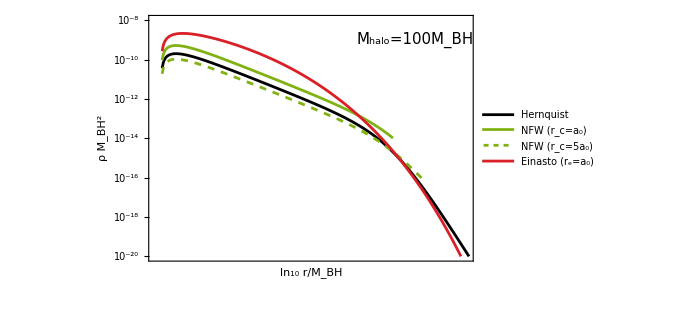

./plot/Fig1.pdf

```mathematica
Show[ListLogPlot[{rhoHQ,rhoNFW,rhoNFW2,rhoEin},Joined->True,Frame->True,FrameLabel->{{Style["ρ M_BH^2",22],None},{Style["ln_10 r/M_BH",22],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotRange->{{Log10[1.5],6.5},{ 10^-20,10^-8}},PlotLegends->Placed[{Style["Hernquist",13],Style["NFW (r_c=a_0)",13],Style["NFW (r_c=5a_0)",13],Style["Einasto (r_e=a_0)",13],Style["Einasto (r_e=a_0)",13]},Scaled[{0.22,0.25}]],PlotStyle->{Directive[Black,AbsoluteThickness[2]],Directive[Comb1[[2]],AbsoluteThickness[2]],Directive[Comb1[[2]],Dashing[{0.01,0.01}],AbsoluteThickness[2]],Directive[Comb2[[1]],AbsoluteThickness[2]],Directive[Comb2[[1]],Dashing[{0.015,0.015}],AbsoluteThickness[2]]},FrameTicks->{{xl,xr},{xb,xu}},Epilog->{leg["M_halo=100M_BH",15,0,0.82,0.9,Black]}]]

Export["./plot/Fig1.pdf",%]
```

```mathematica
leg["a_0=10^5M_BH",15,90,0.73,0.8,Black],leg["5a_0",15,90,0.85,0.9,Black]
```

```mathematica
ListLogPlot[{{{Log10[10^5],10^-22},{Log10[10^5],10^-8}},{{Log10[5 10^5],10^-22},{Log10[5 10^5],10^-8}}},Joined->True,PlotStyle->Directive[Gray,Dashing[{0.015,0.015}],AbsoluteThickness[1]]]
```

## Metric

```mathematica
ρHQmetric1=background["HQ",10^3,10^6,10^13][[1,{1,3}]];
ρHQmetric3=background["HQ",10,10^4,10^13][[1,{1,3}]];
```

```mathematica
ρNFWmetric1=background["NFW",10^3,{10^6,5 10^6},10^13][[1,{1,3}]];
ρNFWmetric3=background["NFW",10,{10^4,5 10^4},10^13][[1,{1,3}]];
```

```mathematica
ρEinmetric1=background["Ein",10^3,{10^6,10^13},10^13][[1,{1,3}]];
ρEinmetric3=background["Ein",10,{10^4,10^13},10^13][[1,{1,3}]];
```

```mathematica
f1H[x_]=ρHQmetric1[[1,2]][x];
f3H[x_]=ρHQmetric3[[1,2]][x];

f1N[x_]=ρNFWmetric1[[1,2]][x];
f3N[x_]=ρNFWmetric3[[1,2]][x];

f1E[x_]=ρEinmetric1[[1,2]][x];
f3E[x_]=ρEinmetric3[[1,2]][x];
```

```mathematica
m1H[x_]=ρHQmetric1[[2,2]][x];
m3H[x_]=ρHQmetric3[[2,2]][x];

m1N[x_]=ρNFWmetric1[[2,2]][x];
m3N[x_]=ρNFWmetric3[[2,2]][x];

m1E[x_]=ρEinmetric1[[2,2]][x];
m3E[x_]=ρEinmetric3[[2,2]][x];
```

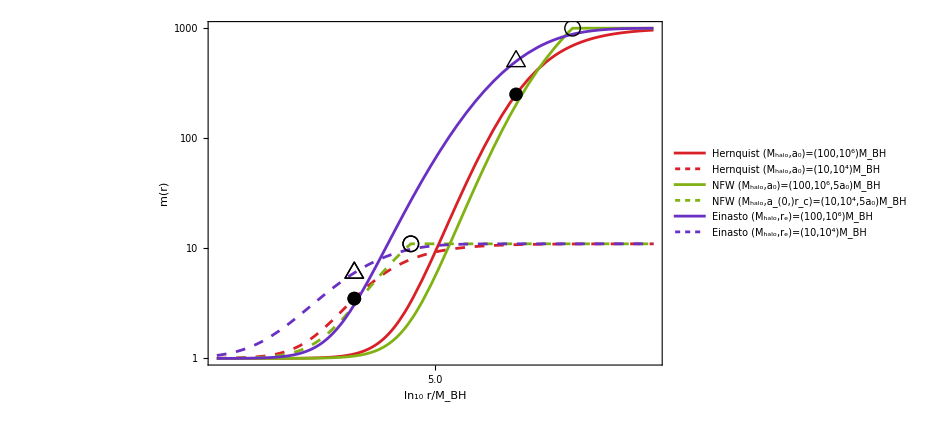

./plot/Fig2a.pdf

```mathematica
xl=Join[Table[{i,,{0.012,0}},{i,1,9}],Table[{10i,,{0.012,0}},{i,1,9}],Table[{100i,,{0.012,0}},{i,1,9}],{{1,"1",{0.02,0}},{10,"10",{0.02,0}},{100,"10^2",{0.02,0}},{1000,"10^3",{0.02,0}}}];
xr=Join[Table[{i,,{0.012,0}},{i,1,9}],Table[{10i,,{0.012,0}},{i,1,9}],Table[{100i,,{0.012,0}},{i,1,9}],{}];

xb=Join[Table[{1i/5,,{0.012,0}},{i,0,100}],Table[{1i,Integerise[1i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{1i/5,,{0.012,0}},{i,0,100}],Table[{1i,,{0.02,0}},{i,0,100}]];

Show[LogPlot[{m1H[10^x],m3H[10^x],m1N[10^x],m3N[10^x],m1E[10^x],m3E[10^x]},{x,Log10[200],Log10[5 10^7]},Frame->True,PlotRange->All,PlotStyle->{Directive[Comb2[[1]],AbsoluteThickness[2]],Directive[Comb2[[1]],Dashing[{0.01,0.01}],AbsoluteThickness[2]],Directive[Comb1[[2]],AbsoluteThickness[2]],Directive[Comb1[[2]],Dashing[{0.01,0.01}],AbsoluteThickness[2]],Directive[Comb3[[2]],AbsoluteThickness[2]],Directive[Comb3[[2]],Dashing[{0.01,0.01}],AbsoluteThickness[2]]},FrameLabel->{{Style["m(r)",26,Italic],None},{Style["ln_10 r/M_BH",22],None}},
ImageSize->700,
FrameStyle->Directive[17,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["Hernquist (M_halo,a_0)=(100,10^6)M_BH",13],Style["Hernquist (M_halo,a_0)=(10,10^4)M_BH",13],Style["NFW (M_halo,a_0)=(100,10^6,5a_0)M_BH",13],Style["NFW (M_halo,a_(0,)r_c)=(10,10^4,5a_0)M_BH",13],Style["Einasto (M_halo,r_e)=(100,10^6)M_BH",13],Style["Einasto (M_halo,r_e)=(10,10^4)M_BH",13]},Scaled[{0.25,0.76}]],ImagePadding->{{70, 50}, {55, 35}},FrameTicks->{{xl,xr},{xb,xu}},Axes->False],ListLogPlot[{{{Log10[10^6],m1H[10^6]},{Log10[10^4],m3H[10^4]}},{{Log10[5 10^6],m1N[5 10^6]},{Log10[5 10^4],m3N[5 10^4]}},{{Log10[10^6],m1E[10^6]},{Log10[10^4],m3E[10^4]}}},PlotStyle->{Black},PlotMarkers->{{"●",14},{"○",16},{"△",22}}]]

Export["./plot/Fig2a.pdf",%]
```

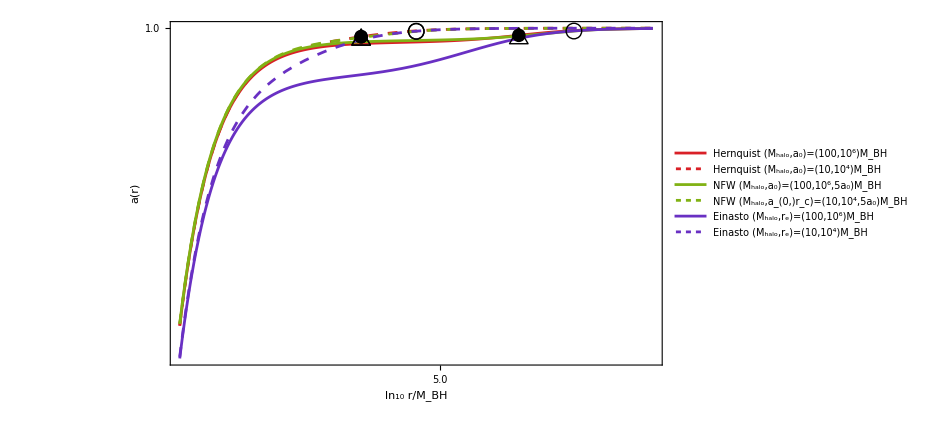

./plot/Fig2b.pdf

```mathematica
xl=Join[Table[{0.9+0.01i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.01i,Integerise[0.9+0.01i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9+0.01i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.01i,,{0.02,0}},{i,0,100}]];

Show[Plot[{f1H[10^x],f3H[10^x],f1N[10^x],f3N[10^x],f1E[10^x],f3E[10^x]},{x,Log10[50],Log10[5 10^7]},Frame->True,PlotRange->All,PlotStyle->{Directive[Comb2[[1]],AbsoluteThickness[2]],Directive[Comb2[[1]],Dashing[{0.01,0.01}],AbsoluteThickness[2]],Directive[Comb1[[2]],AbsoluteThickness[2]],Directive[Comb1[[2]],Dashing[{0.01,0.01}],AbsoluteThickness[2]],Directive[Comb3[[2]],AbsoluteThickness[2]],Directive[Comb3[[2]],Dashing[{0.01,0.01}],AbsoluteThickness[2]]},FrameLabel->{{Style["a(r)",26,Italic],None},{Style["ln_10 r/M_BH",22],None}},
ImageSize->700,
FrameStyle->Directive[17,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["Hernquist (M_halo,a_0)=(100,10^6)M_BH",13],Style["Hernquist (M_halo,a_0)=(10,10^4)M_BH",13],Style["NFW (M_halo,a_0)=(100,10^6,5a_0)M_BH",13],Style["NFW (M_halo,a_(0,)r_c)=(10,10^4,5a_0)M_BH",13],Style["Einasto (M_halo,r_e)=(100,10^6)M_BH",13],Style["Einasto (M_halo,r_e)=(10,10^4)M_BH",13]},Scaled[{0.75,0.3}]],ImagePadding->{{70, 50}, {55, 35}},FrameTicks->{{xl,xr},{xb,xu}},Axes->False],ListPlot[{{{Log10[10^6],f1H[10^6]},{Log10[10^4],f3H[10^4]}},{{Log10[5 10^6],f1N[5 10^6]},{Log10[5 10^4],f3N[5 10^4]}},{{Log10[10^6],f1E[10^6]},{Log10[10^4],f3E[10^4]}}},PlotStyle->{Black},PlotMarkers->{{"●",14},{"○",16},{"△",22}}]]

Export["./plot/Fig2b.pdf",%]
```

## Light Ring

#### Hernquist

```mathematica
nn=30;
```

```mathematica
masses=Range[2,6,(6-2)/nn];
LRHQa0d7={10^#/10^7,background["HQ",10^#,10^7,10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[1,5,(5-1)/nn];
LRHQa0d6={10^#/10^6,background["HQ",10^#,10^6,10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[0,4,(4-0)/nn];
LRHQa0d5={10^#/10^5,background["HQ",10^#,10^5,10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[-1,3,(3-(-1))/nn];
LRHQa0d4={10^#/10^4,background["HQ",10^#,10^4,10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[-2,2,(2-(-2))/nn];
LRHQa0d3={10^#/10^3,background["HQ",10^#,10^3,10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[-3,1,(1-(-3))/nn];
LRHQa0d2={10^#/10^2,background["HQ",10^#,10^2,10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[-4,0,(0-(-4))/nn];
LRHQa0d1={10^#/10,background["HQ",10^#,10,10^13][[2,3]]}&/@masses;
```

```mathematica
Export["./data/LR_HQ.mx",{LRHQa0d1,LRHQa0d2,LRHQa0d3,LRHQa0d4,LRHQa0d5,LRHQa0d6,LRHQa0d7}]
```

./data/LR_HQ.mx

```mathematica
{LRHQa0d1,LRHQa0d2,LRHQa0d3,LRHQa0d4,LRHQa0d5,LRHQa0d6,LRHQa0d7}=Import["./data/LR_HQ.mx"];
```

```mathematica
datatot[n_]:=Join[
Thread[{LRHQa0d7[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn][[1;;n]],(3Sqrt[3])LRHQa0d7[[1;;n,2]]}],
Thread[{LRHQa0d6[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn][[1;;n]],(3Sqrt[3])LRHQa0d6[[1;;n,2]]}],
Thread[{LRHQa0d5[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn][[1;;n]],(3Sqrt[3])LRHQa0d5[[1;;n,2]]}],
Thread[{LRHQa0d4[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn][[1;;n]],(3Sqrt[3])LRHQa0d4[[1;;n,2]]}],Thread[{LRHQa0d3[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn][[1;;n]],(3Sqrt[3])LRHQa0d3[[1;;n,2]]}],Thread[{LRHQa0d2[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn][[1;;n]],(3Sqrt[3])LRHQa0d2[[1;;n,2]]}]];
```

```mathematica
FindFit[datatot[nn+1][[All,2;;-1]],1-α x/z+β x^2/z^2+γ x/z^2,{α,β,γ},{z,x}]
```

{α→0.999888783132603884040901,β→0.168294368320487262612291,γ→2.79282285861112426686239}

```mathematica
pos=Intersection[Flatten[Position[N[datatot[nn+1][[All,1]]],xx_ /; xx<0.01]],Flatten[Position[N[datatot[nn+1][[All,3]]],xx_ /; xx>1]]];
fit1[x_,z_]=1-α x/z+β x^2/z^2+γ x/z^2//.FindFit[datatot[nn+1][[pos,2;;-1]],1-α x/z+β x^2/z^2+γ x/z^2,{α,β,γ},{z,x}]

fit2[x_,z_]=1-α x/z+β x^2/z^2+γ x/z^2//.FindFit[datatot[nn+1][[pos,2;;-1]],1-α x/z,{α,β,γ},{z,x}]
```

1+(2.97993589899577540322588 x)/z^2+(0.16670615837910455943126 x^2)/z^2-(0.999998447470527854308884 x)/z

1-(0.998249930890906087327455 x)/z

```mathematica
Abs[fit2[datatot[nn+1][[pos,3]],datatot[nn+1][[pos,2]]]/datatot[nn+1][[pos,4]]-1]100//Max
```

0.002300006486675926672

```mathematica
dataHQ={
Thread[{LRHQa0d6[[1;;nn+1,1]],(3Sqrt[3])LRHQa0d6[[1;;nn+1,2]]}],
Thread[{LRHQa0d5[[1;;nn+1,1]],(3Sqrt[3])LRHQa0d5[[1;;nn+1,2]]}],
Thread[{LRHQa0d4[[1;;nn+1,1]],(3Sqrt[3])LRHQa0d4[[1;;nn+1,2]]}],
Thread[{LRHQa0d3[[1;;nn+1,1]],(3Sqrt[3])LRHQa0d3[[1;;nn+1,2]]}],
Thread[{LRHQa0d2[[1;;nn+1,1]],(3Sqrt[3])LRHQa0d2[[1;;nn+1,2]]}],
Thread[{LRHQa0d1[[1;;nn+1,1]],(3Sqrt[3])LRHQa0d1[[1;;nn+1,2]]}]};
```

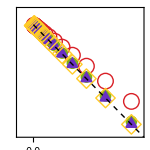

```mathematica
xl=Join[Table[{0.9984+0.0004i/5,,{0.012,0}},{i,0,100}],Table[{0.9984+0.0004i,Integerise[0.9984+0.0004i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9984+0.0004i/5,,{0.012,0}},{i,0,100}],Table[{0.9984+0.0004i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,Integerise[0.0005i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,,{0.02,0}},{i,0,100}]];

inset=Show[ListPlot[{dataHQ[[-1]],dataHQ[[-2]],dataHQ[[-3]],dataHQ[[-4]]},PlotMarkers->{{"○",16},{"●",12},{"▲",16},{"◇",20}},PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]},PlotRange->{{-0.0002,0.0015},{0.9985,1.0002}},Frame->True,Axes->False,FrameStyle->Directive[10,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],AspectRatio->1,ImageSize->150,ImagePadding->{{35, 15}, {20, 10}},FrameTicks->{{xl,xr},{xb,xu}}],Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]}]]
```

```mathematica
{0.01,0.02,0.04,0.06,0.08,0.1} 10^4
```

{100.,200.,400.,600.,800.,1000.}

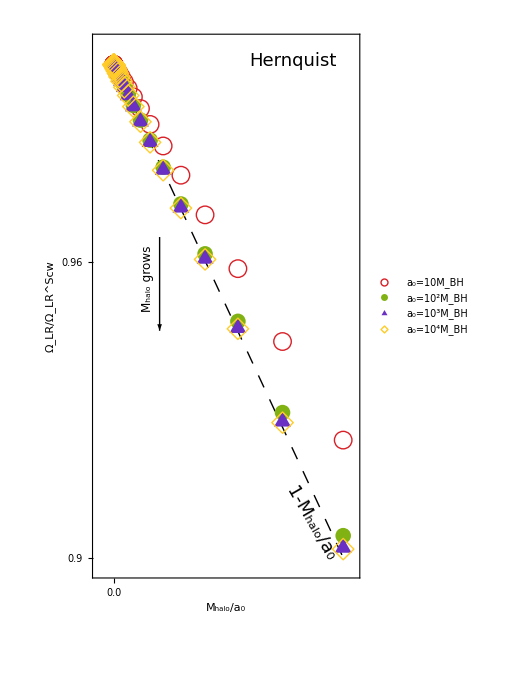

```mathematica
xl=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,Rotate[Integerise[0.9+0.02i],45Degree],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,Integerise[0.02i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,,{0.02,0}},{i,0,100}]];

xu2=Table[{{0.01,0.02,0.04,0.06,0.08,0.1}[[i]],Style[ToString[{"100","200","400","600","800","1000"}[[i]]],13],{0.02,0}},{i,1,6}];

p1=Show[Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{Style["Ω_LR/Ω_LR^Scw",22],None},{Style["M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["Hernquist",18,0,0.75,0.95,Black],leg["M_halo grows",12,90,0.205,0.55,Black],Inset[inset,Scaled[{0.68,0.78}]],leg["1-M_halo/a_0",18,-60,0.82,0.1,Black]},Axes->False,
FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-0.007,0.105},{0.898,1.004}}],
ListPlot[{dataHQ[[-1]],dataHQ[[-2]],dataHQ[[-3]],dataHQ[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10M_BH",14],Style["a_0=10^2M_BH",14],Style["a_0=10^3M_BH",14],Style["a_0=10^4M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}],Graphics[Arrow[{{0.02,0.965},{0.02,0.946}}]]]
```

```mathematica
dataHQ={
Thread[{Log10[LRHQa0d6[[1;;nn+1,1]]],(3Sqrt[3])LRHQa0d6[[1;;nn+1,2]]}],
Thread[{Log10[LRHQa0d5[[1;;nn+1,1]]],(3Sqrt[3])LRHQa0d5[[1;;nn+1,2]]}],
Thread[{Log10[LRHQa0d4[[1;;nn+1,1]]],(3Sqrt[3])LRHQa0d4[[1;;nn+1,2]]}],
Thread[{Log10[LRHQa0d3[[1;;nn+1,1]]],(3Sqrt[3])LRHQa0d3[[1;;nn+1,2]]}],
Thread[{Log10[LRHQa0d2[[1;;nn+1,1]]],(3Sqrt[3])LRHQa0d2[[1;;nn+1,2]]}],
Thread[{Log10[LRHQa0d1[[1;;nn+1,1]]],(3Sqrt[3])LRHQa0d1[[1;;nn+1,2]]}]};
```

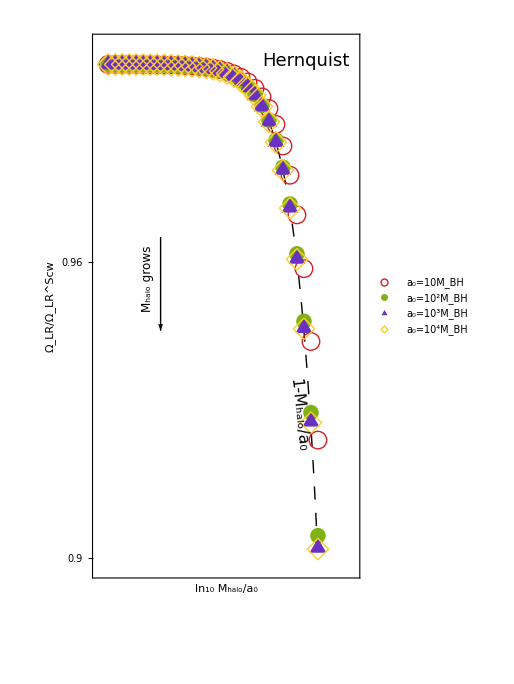

```mathematica
xb=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,Integerise[-6+1i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,,{0.02,0}},{i,0,100}]];

xu2=Table[{Log10[{0.0001,0.001,0.01,0.1}][[i]],Style[ToString[{"10","100","1000","1000"}[[i]]],13],{0.02,0}},{i,1,4}];

p1bis=Show[Plot[{1-10^z},{z,Log10[10^-5],Log10[0.1]},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{Style["Ω_LR/Ω_LR^Scw",22],None},{Style["ln_10 M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["Hernquist",18,0,0.8,0.95,Black],leg["M_halo grows",12,90,0.205,0.55,Black],Inset[inset,Scaled[{0.3,0.78}]],leg["1-M_halo/a_0",16,-84,0.77,0.3,Black]},Axes->False,PlotRange->{{-5.2,-0.3},{0.898,1.004}},FrameTicks->{{xl,xr},{xb,xu2}}],
ListPlot[{dataHQ[[-1]],dataHQ[[-2]],dataHQ[[-3]],dataHQ[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10M_BH",14],Style["a_0=10^2M_BH",14],Style["a_0=10^3M_BH",14],Style["a_0=10^4M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}],Graphics[Arrow[{{-4,0.965},{-4,0.946}}]]]
```

#### NFW

```mathematica
nn=30;
```

```mathematica
masses=Range[2,6,(6-2)/nn];
LRNFWa0d7={10^#/10^7,background["NFW",10^#,{10^7,10^7},10^13][[2,3]]}&/@masses;
LRNFWa0d7v2={10^#/10^7,background["NFW",10^#,{10^7,2 10^7},10^13][[2,3]]}&/@masses;
LRNFWa0d7v3={10^#/10^7,background["NFW",10^#,{10^7,3 10^7},10^13][[2,3]]}&/@masses;
LRNFWa0d7v4={10^#/10^7,background["NFW",10^#,{10^7,4 10^7},10^13][[2,3]]}&/@masses;
LRNFWa0d7v5={10^#/10^7,background["NFW",10^#,{10^7,5 10^7},10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[1,5,(5-1)/nn];
LRNFWa0d6={10^#/10^6,background["NFW",10^#,{10^6,10^6},10^13][[2,3]]}&/@masses;
LRNFWa0d6v2={10^#/10^6,background["NFW",10^#,{10^6,2 10^6},10^13][[2,3]]}&/@masses;
LRNFWa0d6v3={10^#/10^6,background["NFW",10^#,{10^6,3 10^6},10^13][[2,3]]}&/@masses;
LRNFWa0d6v4={10^#/10^6,background["NFW",10^#,{10^6,4 10^6},10^13][[2,3]]}&/@masses;
LRNFWa0d6v5={10^#/10^6,background["NFW",10^#,{10^6,5 10^6},10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[0,4,(4-0)/nn];
LRNFWa0d5={10^#/10^5,background["NFW",10^#,{10^5,10^5},10^13][[2,3]]}&/@masses;
LRNFWa0d5v2={10^#/10^5,background["NFW",10^#,{10^5,2 10^5},10^13][[2,3]]}&/@masses;
LRNFWa0d5v3={10^#/10^5,background["NFW",10^#,{10^5,3 10^5},10^13][[2,3]]}&/@masses;
LRNFWa0d5v4={10^#/10^5,background["NFW",10^#,{10^5,4 10^5},10^13][[2,3]]}&/@masses;
LRNFWa0d5v5={10^#/10^5,background["NFW",10^#,{10^5,5 10^5},10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[-1,3,(3-(-1))/nn];
LRNFWa0d4={10^#/10^4,background["NFW",10^#,{10^4,10^4},10^13][[2,3]]}&/@masses;
LRNFWa0d4v2={10^#/10^4,background["NFW",10^#,{10^4,2 10^4},10^13][[2,3]]}&/@masses;
LRNFWa0d4v3={10^#/10^4,background["NFW",10^#,{10^4,3 10^4},10^13][[2,3]]}&/@masses;
LRNFWa0d4v4={10^#/10^4,background["NFW",10^#,{10^4,4 10^4},10^13][[2,3]]}&/@masses;
LRNFWa0d4v5={10^#/10^4,background["NFW",10^#,{10^4,5 10^4},10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[-2,2,(2-(-2))/nn];
LRNFWa0d3={10^#/10^3,background["NFW",10^#,{10^3,10^3},10^13][[2,3]]}&/@masses;
LRNFWa0d3v2={10^#/10^3,background["NFW",10^#,{10^3,2 10^3},10^13][[2,3]]}&/@masses;
LRNFWa0d3v3={10^#/10^3,background["NFW",10^#,{10^3,3 10^3},10^13][[2,3]]}&/@masses;
LRNFWa0d3v4={10^#/10^3,background["NFW",10^#,{10^3,4 10^3},10^13][[2,3]]}&/@masses;
LRNFWa0d3v5={10^#/10^3,background["NFW",10^#,{10^3,5 10^3},10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[-3,1,(1-(-3))/nn];
LRNFWa0d2={10^#/10^2,background["NFW",10^#,{10^2,10^2},10^13][[2,3]]}&/@masses;
LRNFWa0d2v2={10^#/10^2,background["NFW",10^#,{10^2,2 10^2},10^13][[2,3]]}&/@masses;
LRNFWa0d2v3={10^#/10^2,background["NFW",10^#,{10^2,3 10^2},10^13][[2,3]]}&/@masses;
LRNFWa0d2v4={10^#/10^2,background["NFW",10^#,{10^2,4 10^2},10^13][[2,3]]}&/@masses;
LRNFWa0d2v5={10^#/10^2,background["NFW",10^#,{10^2,5 10^2},10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[-4,0,(0-(-4))/nn];
LRNFWa0d1={10^#/10,background["NFW",10^#,{10,10},10^13][[2,3]]}&/@masses;
LRNFWa0d1v2={10^#/10,background["NFW",10^#,{10,2 10},10^13][[2,3]]}&/@masses;
LRNFWa0d1v3={10^#/10,background["NFW",10^#,{10,3 10},10^13][[2,3]]}&/@masses;
LRNFWa0d1v4={10^#/10,background["NFW",10^#,{10,4 10},10^13][[2,3]]}&/@masses;
LRNFWa0d1v5={10^#/10,background["NFW",10^#,{10,5 10},10^13][[2,3]]}&/@masses;
```

```mathematica
Export["./data/LR_NFW.mx",
{{LRNFWa0d7,LRNFWa0d6,LRNFWa0d5,LRNFWa0d4,LRNFWa0d3,LRNFWa0d2,LRNFWa0d1},
{LRNFWa0d7v2,LRNFWa0d6v2,LRNFWa0d5v2,LRNFWa0d4v2,LRNFWa0d3v2,LRNFWa0d2v2,LRNFWa0d1v2},{LRNFWa0d7v3,LRNFWa0d6v3,LRNFWa0d5v3,LRNFWa0d4v3,LRNFWa0d3v3,LRNFWa0d2v3,LRNFWa0d1v3},{LRNFWa0d7v4,LRNFWa0d6v4,LRNFWa0d5v4,LRNFWa0d4v4,LRNFWa0d3v4,LRNFWa0d2v4,LRNFWa0d1v4},{LRNFWa0d7v5,LRNFWa0d6v5,LRNFWa0d5v5,LRNFWa0d4v5,LRNFWa0d3v5,LRNFWa0d2v5,LRNFWa0d1v5}}]
```

./data/LR_NFW.mx

```mathematica
{{LRNFWa0d7,LRNFWa0d6,LRNFWa0d5,LRNFWa0d4,LRNFWa0d3,LRNFWa0d2,LRNFWa0d1},
{LRNFWa0d7v2,LRNFWa0d6v2,LRNFWa0d5v2,LRNFWa0d4v2,LRNFWa0d3v2,LRNFWa0d2v2,LRNFWa0d1v2},{LRNFWa0d7v3,LRNFWa0d6v3,LRNFWa0d5v3,LRNFWa0d4v3,LRNFWa0d3v3,LRNFWa0d2v3,LRNFWa0d1v3},{LRNFWa0d7v4,LRNFWa0d6v4,LRNFWa0d5v4,LRNFWa0d4v4,LRNFWa0d3v4,LRNFWa0d2v4,LRNFWa0d1v4},{LRNFWa0d7v5,LRNFWa0d6v5,LRNFWa0d5v5,LRNFWa0d4v5,LRNFWa0d3v5,LRNFWa0d2v5,LRNFWa0d1v5}}=Import["./data/LR_NFW.mx"];
```

```mathematica
datatot[n_]:=Join[
Thread[{LRNFWa0d5[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(3Sqrt[3])LRNFWa0d5[[1;;n,2]]}],
Thread[{LRNFWa0d4[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(3Sqrt[3])LRNFWa0d4[[1;;n,2]]}],Thread[{LRNFWa0d3[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(3Sqrt[3])LRNFWa0d3[[1;;n,2]]}],
Thread[{LRNFWa0d2[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(3Sqrt[3])LRNFWa0d2[[1;;n,2]]}]]//N
```

```mathematica
datatot5[n_]:=Join[
Thread[{LRNFWa0d5v5[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(3Sqrt[3])LRNFWa0d5v5[[1;;n,2]]}],
Thread[{LRNFWa0d4v5[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(3Sqrt[3])LRNFWa0d4v5[[1;;n,2]]}],Thread[{LRNFWa0d3v5[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(3Sqrt[3])LRNFWa0d3v5[[1;;n,2]]}],
Thread[{LRNFWa0d2v5[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(3Sqrt[3])LRNFWa0d2v5[[1;;n,2]]}]]//N
```

```mathematica
pos=Intersection[Flatten[Position[N[datatot[nn+1][[All,1]]],xx_ /; xx<0.1]],Flatten[Position[N[datatot[nn+1][[All,2]]],xx_ /; xx>1]]];
fit1[x_,z_]=1-α x/z+β x^2/z^2+γ x/z^2//.FindFit[datatot[nn+1][[pos,2;;-1]],1-α x/z+β x^2/z^2+γ x/z^2,{α,β,γ},{z,x}]
fit2[x_,z_]=1-α x/z//.FindFit[datatot[nn+1][[pos,2;;-1]],1-α x/z,{α,β,γ},{z,x}]
```

1-(0.912777 x)/z^2+(0.498738 x^2)/z^2-(2.58873 x)/z

1-(2.56329 x)/z

```mathematica
datatot[nn+1][[pos,1;;-1]][[1;;2]]//TableForm
```

0.00001 | 100000. | 1. | 0.999974
0.0000135936 | 100000. | 1.35936 | 0.999965

```mathematica
Abs[fit2[datatot[nn+1][[pos,3]],datatot[nn+1][[pos,2]]]/datatot[nn+1][[pos,4]]-1]//Max
```

0.00105436

```mathematica
dataNFW={
Thread[{LRNFWa0d5[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d5[[1;;nn+1,2]]}],
Thread[{LRNFWa0d4[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d4[[1;;nn+1,2]]}],
Thread[{LRNFWa0d3[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d3[[1;;nn+1,2]]}],
Thread[{LRNFWa0d2[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d2[[1;;nn+1,2]]}],
Thread[{LRNFWa0d1[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d1[[1;;nn+1,2]]}]};

dataNFWv2={
Thread[{LRNFWa0d5v2[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d5v2[[1;;nn+1,2]]}],
Thread[{LRNFWa0d4v2[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d4v2[[1;;nn+1,2]]}],
Thread[{LRNFWa0d3v2[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d3v2[[1;;nn+1,2]]}],
Thread[{LRNFWa0d2v2[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d2v2[[1;;nn+1,2]]}],
Thread[{LRNFWa0d1v2[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d1v2[[1;;nn+1,2]]}]};

dataNFWv5={
Thread[{LRNFWa0d5v5[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d5v5[[1;;nn+1,2]]}],
Thread[{LRNFWa0d4v5[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d4v5[[1;;nn+1,2]]}],
Thread[{LRNFWa0d3v5[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d3v5[[1;;nn+1,2]]}],
Thread[{LRNFWa0d2v5[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d2v5[[1;;nn+1,2]]}],
Thread[{LRNFWa0d1v5[[1;;nn+1,1]],(3Sqrt[3])LRNFWa0d1v5[[1;;nn+1,2]]}]};
```

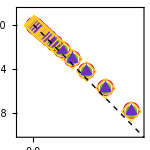

```mathematica
xl=Join[Table[{0.9984+0.0004i/5,,{0.012,0}},{i,0,100}],Table[{0.9984+0.0004i,Integerise[0.9984+0.0004i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9984+0.0004i/5,,{0.012,0}},{i,0,100}],Table[{0.9984+0.0004i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,Integerise[0.0005i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,,{0.02,0}},{i,0,100}]];

xu2=Table[{{0.01,0.02,0.04,0.06,0.08,0.1}[[i]],Style[ToString[{"100","200","400","600","800","1000"}[[i]]],13],{0.02,0}},{i,1,6}];

inset2=Show[ListPlot[{dataNFWv5[[-2]],dataNFWv5[[-3]],dataNFWv5[[-4]],dataNFWv5[[-5]]},PlotMarkers->{{"○",16},{"●",12},{"▲",16},{"◇",20}},PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]},PlotRange->{{-0.0002,0.0015},{0.9985,1.0002}},Frame->True,Axes->False,FrameStyle->Directive[10,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],AspectRatio->1,ImageSize->150,ImagePadding->{{10, 35}, {20, 10}},FrameTicks->{{xr,xl},{xb,xu}}],Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]}]]
```

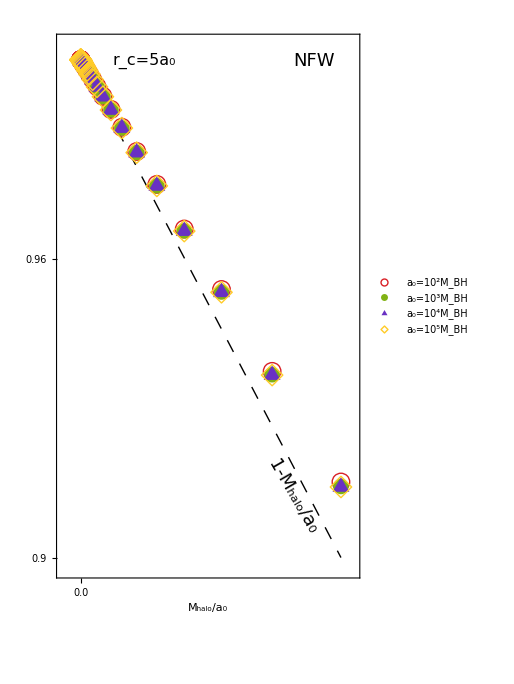

```mathematica
xl=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,Rotate[Integerise[0.9+0.02i],45Degree],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,Integerise[0.02i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,,{0.02,0}},{i,0,100}]];

xu2=Table[{{0.01,0.02,0.04,0.06,0.08,0.1}[[i]],Style[ToString[{"100","200","400","600","800","1000"}[[i]]],13],{0.02,0}},{i,1,6}];

p2=Show[Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{None,None},{Style["M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",18,-60,0.78,0.15,Black],leg["NFW",18,0,0.85,0.95,Black],leg["r_c=5a_0",16,0,0.29,0.95,Black],Inset[inset2,Scaled[{0.68,0.78}]]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-0.007,0.105},{0.898,1.003}}],
ListPlot[{dataNFWv5[[-2]],dataNFWv5[[-3]],dataNFWv5[[-4]],dataNFWv5[[-5]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^2M_BH",14],Style["a_0=10^3M_BH",14],Style["a_0=10^4M_BH",14],Style["a_0=10^5M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

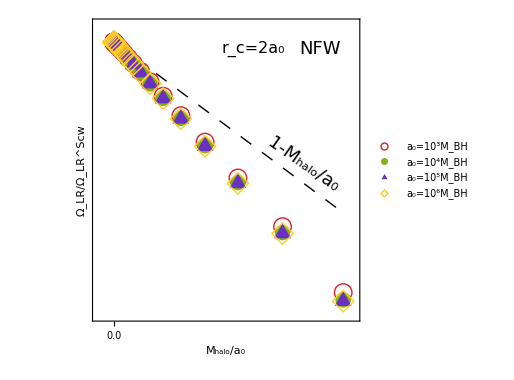

```mathematica
xl=Join[Table[{0.82+0.04i/5,,{0.012,0}},{i,0,100}],Table[{0.82+0.04i,Integerise[0.82+0.04i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.82+0.04i/5,,{0.012,0}},{i,0,100}],Table[{0.82+0.04i,,{0.02,0}},{i,0,100}]];

p22=Show[Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{Style["Ω_LR/Ω_LR^Scw",22],None},{Style["M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",18,-35,0.79,0.52,Black],leg["NFW",18,0,0.85,0.9,Black],leg["r_c=2a_0",16,0,0.6,0.9,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-0.007,0.105},{0.84,1.01}}],
ListPlot[{dataNFWv2[[-1]],dataNFWv2[[-2]],dataNFWv2[[-3]],dataNFWv2[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",12],Style["a_0=10^4M_BH",12],Style["a_0=10^5M_BH",12],Style["a_0=10^6M_BH",12]},Scaled[{0.22,0.22}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

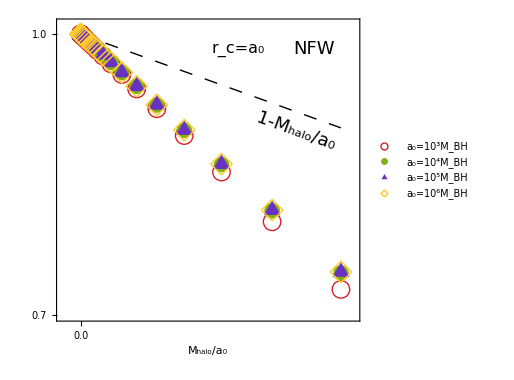

```mathematica
xl=Join[Table[{0.7+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.7+0.05i,Integerise[0.7+0.05i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.7+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.7+0.05i,,{0.02,0}},{i,0,100}]];

p23=Show[Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{None,None},{Style["M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",18,-20,0.79,0.63,Black],leg["NFW",18,0,0.85,0.9,Black],leg["r_c=a_0",16,0,0.6,0.9,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-0.007,0.105},{0.7,1.01}}],
ListPlot[{dataNFW[[-1]],dataNFW[[-2]],dataNFW[[-3]],dataNFW[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",12],Style["a_0=10^4M_BH",12],Style["a_0=10^5M_BH",12],Style["a_0=10^6M_BH",12]},Scaled[{0.22,0.22}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

```mathematica
dataNFW={
Thread[{Log10[LRNFWa0d5[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d5[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d4[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d4[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d3[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d3[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d2[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d2[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d1[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d1[[1;;nn+1,2]]}]};

dataNFWv2={
Thread[{Log10[LRNFWa0d5v2[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d5v2[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d4v2[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d4v2[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d3v2[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d3v2[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d2v2[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d2v2[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d1v2[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d1v2[[1;;nn+1,2]]}]};

dataNFWv5={
Thread[{Log10[LRNFWa0d5v5[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d5v5[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d4v5[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d4v5[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d3v5[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d3v5[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d2v5[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d2v5[[1;;nn+1,2]]}],
Thread[{Log10[LRNFWa0d1v5[[1;;nn+1,1]]],(3Sqrt[3])LRNFWa0d1v5[[1;;nn+1,2]]}]};
```

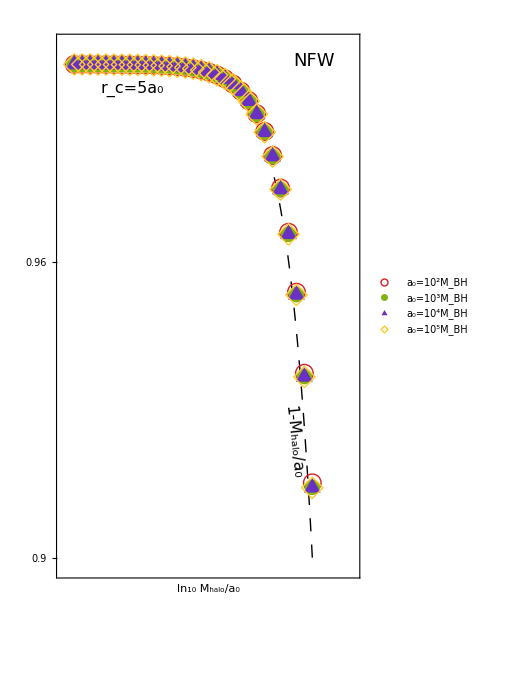

```mathematica
xl=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,Rotate[Integerise[0.9+0.02i],45Degree],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,Integerise[-6+1i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,,{0.02,0}},{i,0,100}]];

xu2=Table[{Log10[{0.0001,0.001,0.01,0.1}][[i]],Style[ToString[{"10","100","1000","1000"}[[i]]],13],{0.02,0}},{i,1,4}];

p2bis=Show[Plot[{1-10^z},{z,Log10[10^-5],Log10[0.1]},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{None,None},{Style["ln_10 M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",16,-84,0.78,0.25,Black],leg["NFW",18,0,0.85,0.95,Black],leg["r_c=5a_0",16,0,0.25,0.9,Black],Inset[inset2,Scaled[{0.3,0.7}]]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-5.2,-0.3},{0.898,1.004}}],
ListPlot[{dataNFWv5[[-2]],dataNFWv5[[-3]],dataNFWv5[[-4]],dataNFWv5[[-5]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^2M_BH",14],Style["a_0=10^3M_BH",14],Style["a_0=10^4M_BH",14],Style["a_0=10^5M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

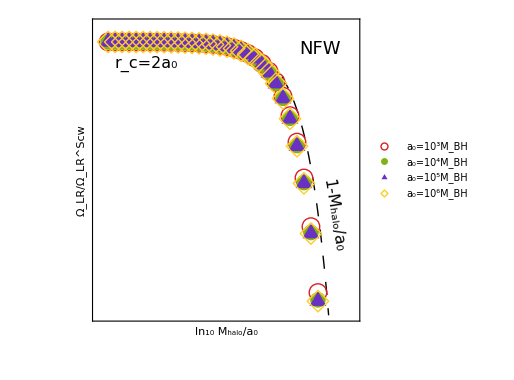

```mathematica
xl=Join[Table[{0.82+0.04i/5,,{0.012,0}},{i,0,100}],Table[{0.82+0.04i,Integerise[0.82+0.04i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.82+0.04i/5,,{0.012,0}},{i,0,100}],Table[{0.82+0.04i,,{0.02,0}},{i,0,100}]];

p22bis=Show[Plot[{1-10^z},{z,Log10[10^-5],Log10[0.2]},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{Style["Ω_LR/Ω_LR^Scw",22],None},{Style["ln_10 M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",16,-81,0.9,0.35,Black],leg["NFW",18,0,0.85,0.9,Black],leg["r_c=2a_0",16,0,0.2,0.85,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-5.2,-0.3},{0.84,1.01}}],
ListPlot[{dataNFWv2[[-1]],dataNFWv2[[-2]],dataNFWv2[[-3]],dataNFWv2[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",12],Style["a_0=10^4M_BH",12],Style["a_0=10^5M_BH",12],Style["a_0=10^6M_BH",12]},Scaled[{0.22,0.22}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

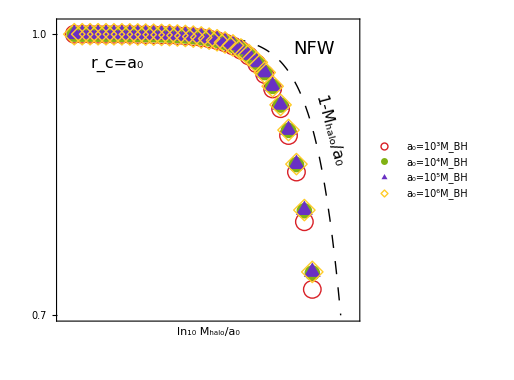

```mathematica
xl=Join[Table[{0.7+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.7+0.05i,Integerise[0.7+0.05i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.7+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.7+0.05i,,{0.02,0}},{i,0,100}]];

p23bis=Show[Plot[{1-10^z},{z,Log10[10^-5],Log10[0.3]},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{None,None},{Style["ln_10 M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",16,-75,0.9,0.63,Black],leg["NFW",18,0,0.85,0.9,Black],leg["r_c=a_0",16,0,0.2,0.85,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-5.2,-0.3},{0.7,1.01}}],
ListPlot[{dataNFW[[-1]],dataNFW[[-2]],dataNFW[[-3]],dataNFW[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",12],Style["a_0=10^4M_BH",12],Style["a_0=10^5M_BH",12],Style["a_0=10^6M_BH",12]},Scaled[{0.22,0.22}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

#### Einasto

```mathematica
nn=30;
```

```mathematica
masses=Range[1,5,(5-1)/nn];
LREina0d6={10^#/10^6,background["Ein",10^#,{10^6,10^13},10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[0,4,(4-0)/nn];
LREina0d5={10^#/10^5,background["Ein",10^#,{10^5,10^13},10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[-1,3,(3-(-1))/nn];
LREina0d4={10^#/10^4,background["Ein",10^#,{10^4,10^13},10^13][[2,3]]}&/@masses;
```

```mathematica
masses=Range[-2,2,(2-(-2))/nn];
LREina0d3={10^#/10^3,background["Ein",10^#,{10^3,10^13},10^13][[2,3]]}&/@masses;
```

```mathematica
Export["./data/LR_Ein.mx",{LREina0d6,LREina0d5,LREina0d4,LREina0d3}]
```

./data/LR_Ein.mx

```mathematica
{LREina0d6,LREina0d5,LREina0d4,LREina0d3}=Import["./data/LR_Ein.mx"];
```

```mathematica
dataEin={
Thread[{LREina0d6[[All,1]],(3Sqrt[3])LREina0d6[[All,2]]}],
Thread[{LREina0d5[[All,1]],(3Sqrt[3])LREina0d5[[All,2]]}],
Thread[{LREina0d4[[All,1]],(3Sqrt[3])LREina0d4[[All,2]]}],
Thread[{LREina0d3[[All,1]],(3Sqrt[3])LREina0d3[[All,2]]}]};
```

```mathematica
FindFit[Partition[Flatten[dataEin],2],a+b xx,{a,b,c},xx];
fitEin[xx_]=a+b xx//.%
```

0.999260624079194615204038-3.18073695890666237635907 xx

```mathematica
Abs[fitEin[Partition[Flatten[dataEin],2][[All,1]]]/Partition[Flatten[dataEin],2][[All,2]]-1];
Position[%,Min[%]][[1,1]]
Partition[Flatten[dataEin],2][[All,1]][[%]]//N
```

82

0.00341455

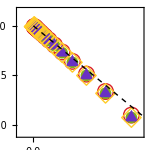

```mathematica
xl=Join[Table[{0.95+0.002i/5,,{0.012,0}},{i,0,1000}],Table[{0.95+0.002i,Integerise[0.95+0.002i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.95+0.002i/5,,{0.012,0}},{i,0,1000}],Table[{0.95+0.002i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,Integerise[0.0005i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,,{0.02,0}},{i,0,100}]];

inset3=Show[ListPlot[{dataEin[[-1]],dataEin[[-2]],dataEin[[-3]],dataEin[[-4]]},PlotMarkers->{{"○",16},{"●",12},{"▲",16},{"◇",20}},PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]},PlotRange->{{-0.0002,0.0015},{0.9945,1.0008}},Frame->True,Axes->False,FrameStyle->Directive[10,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],AspectRatio->1,ImageSize->150,ImagePadding->{{10, 35}, {20, 10}},FrameTicks->{{xr,xl},{xb,xu}}],Plot[{1-3z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]}]]
```

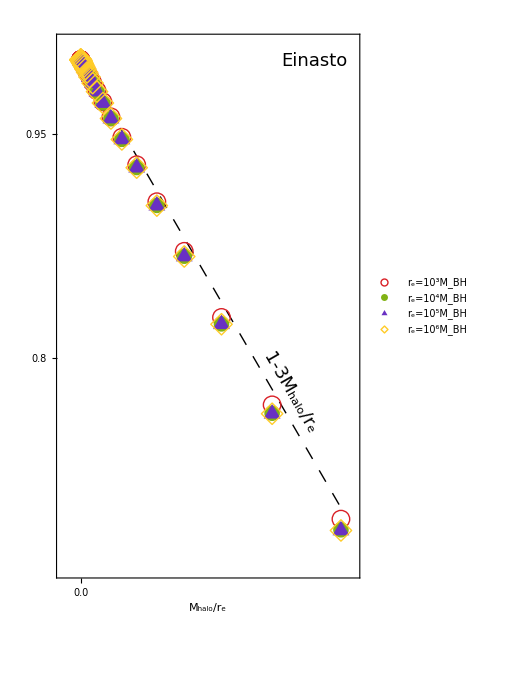

```mathematica
xl=Join[Table[{0.5+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.5+0.05i,Rotate[Integerise[0.5+0.05i],45Degree],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.5+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.5+0.05i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,Integerise[0.02i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,,{0.02,0}},{i,0,100}]];

xu2=Table[{{0.01,0.02,0.04,0.06,0.08,0.1}[[i]],Style[ToString[{"100","200","400","600","800","1000"}[[i]]],13],{0.02,0}},{i,1,6}];

p3=Show[Plot[{1-3z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,FrameLabel->{{None,None},{Style["M_halo/r_e",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{Inset[inset3,Scaled[{0.68,0.78}]],leg["1-3M_halo/r_e",18,-60,0.77,0.34,Black],leg["Einasto",18,0,0.85,0.95,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-0.007,0.105},{0.66,1.01}}],
ListPlot[{dataEin[[-1]],dataEin[[-2]],dataEin[[-3]],dataEin[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["r_e=10^3M_BH",14],Style["r_e=10^4M_BH",14],Style["r_e=10^5M_BH",14],Style["r_e=10^6M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

```mathematica
dataEin={
Thread[{Log10[LREina0d6[[All,1]]],(3Sqrt[3])LREina0d6[[All,2]]}],
Thread[{Log10[LREina0d5[[All,1]]],(3Sqrt[3])LREina0d5[[All,2]]}],
Thread[{Log10[LREina0d4[[All,1]]],(3Sqrt[3])LREina0d4[[All,2]]}],
Thread[{Log10[LREina0d3[[All,1]]],(3Sqrt[3])LREina0d3[[All,2]]}]};
```

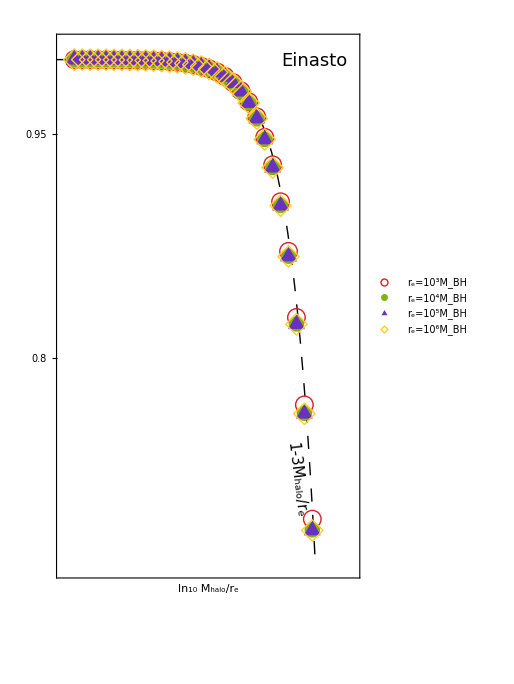

```mathematica
xl=Join[Table[{0.5+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.5+0.05i,Rotate[Integerise[0.5+0.05i],45Degree],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.5+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.5+0.05i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,Integerise[-6+1i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,,{0.02,0}},{i,0,100}]];

xu2=Table[{Log10[{0.0001,0.001,0.01,0.1}][[i]],Style[ToString[{"10","100","1000","1000"}[[i]]],13],{0.02,0}},{i,1,4}];

p3bis=Show[Plot[{1-3 10^z},{z,Log[10^-5],Log[4 10^-1]},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,FrameLabel->{{None,None},{Style["ln_10 M_halo/r_e",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{Inset[inset3,Scaled[{0.3,0.78}]],leg["1-3M_halo/r_e",15,-83,0.79,0.18,Black],leg["Einasto",18,0,0.85,0.95,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-5.2,-0.3},{0.66,1.01}}],
ListPlot[{dataEin[[-1]],dataEin[[-2]],dataEin[[-3]],dataEin[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["r_e=10^3M_BH",14],Style["r_e=10^4M_BH",14],Style["r_e=10^5M_BH",14],Style["r_e=10^6M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

#### Final grouping

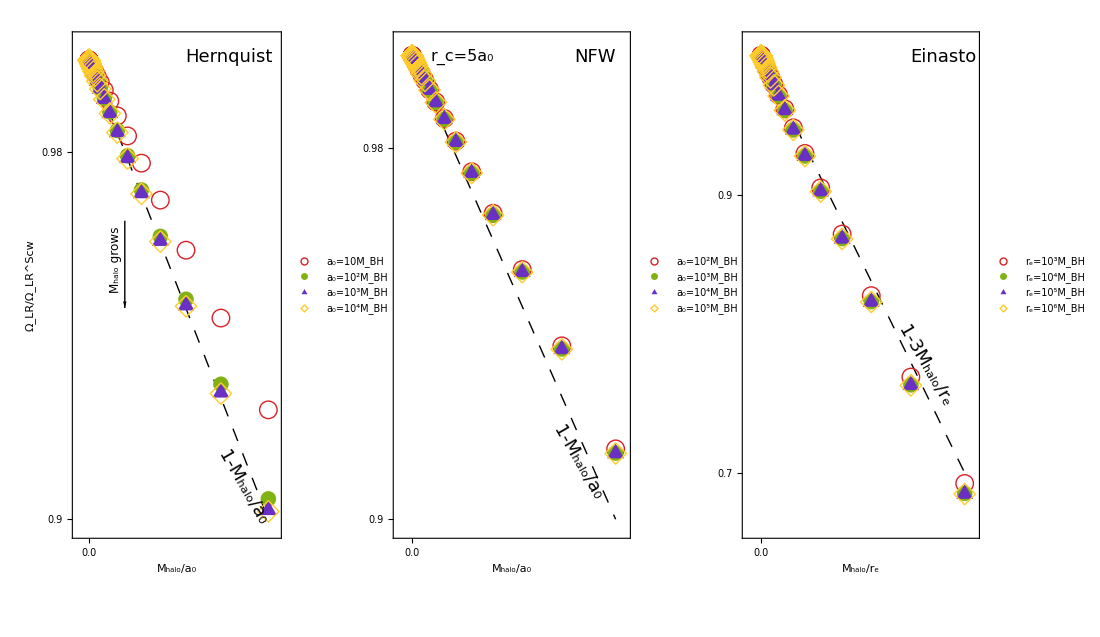

./plot/Fig3a.pdf

```mathematica
GraphicsRow[{p1,p2,p3},ImageSize->1100,Spacings->-50,ImagePadding->{{20,60}, {0, 0}}]
Export["./plot/Fig3a.pdf",%]
```

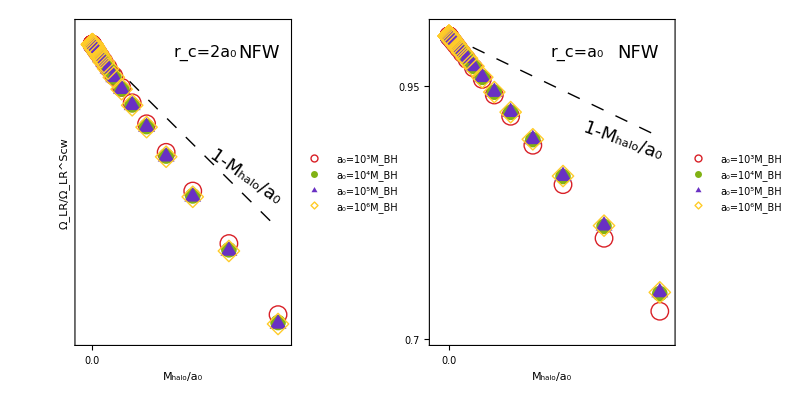

./plot/Fig4a.pdf

```mathematica
GraphicsRow[{p22,p23},ImageSize->800,Spacings->-30,ImagePadding->{{20,60}, {0, 0}}]
Export["./plot/Fig4a.pdf",%]
```

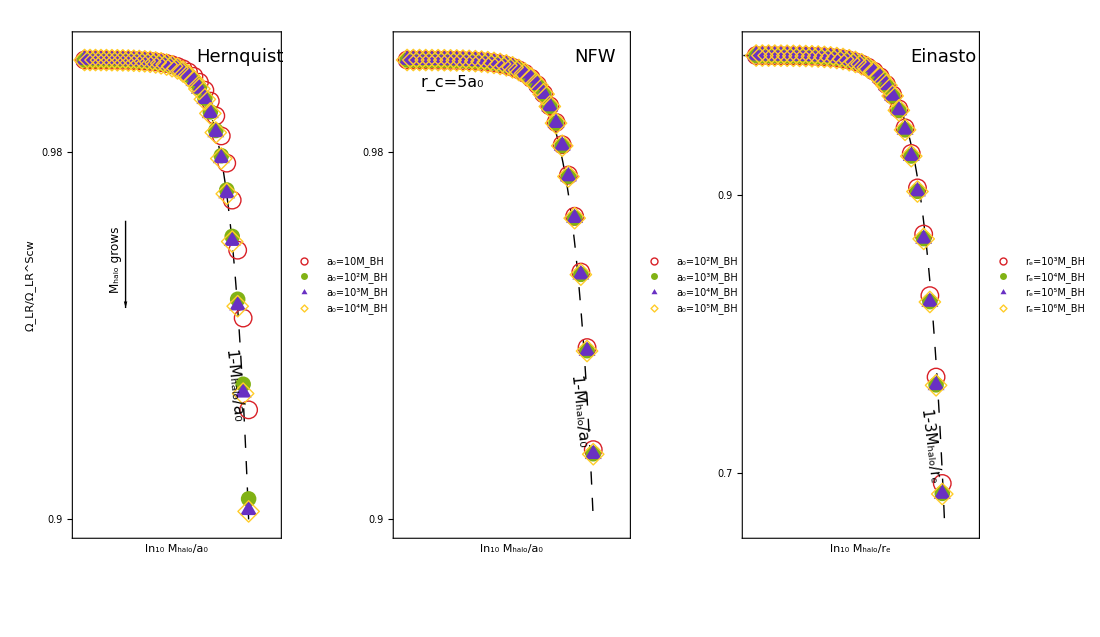

./plot/Fig3abis.pdf

```mathematica
GraphicsRow[{p1bis,p2bis,p3bis},ImageSize->1100,Spacings->-50,ImagePadding->{{20,60}, {0, 0}}]
Export["./plot/Fig3abis.pdf",%]
```

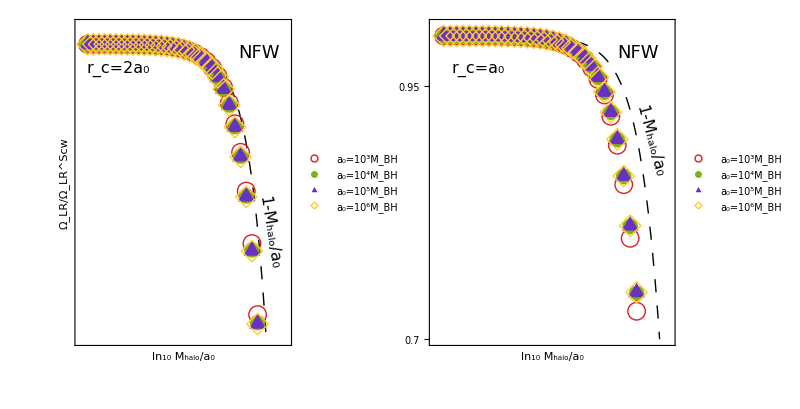

./plot/Fig4abis.pdf

```mathematica
GraphicsRow[{p22bis,p23bis},ImageSize->800,Spacings->-30,ImagePadding->{{20,60}, {0, 0}}]
Export["./plot/Fig4abis.pdf",%]
```

#### Fit for NFW

```mathematica
{{LRNFWa0d7,LRNFWa0d6,LRNFWa0d5,LRNFWa0d4,LRNFWa0d3,LRNFWa0d2,LRNFWa0d1},
{LRNFWa0d7v2,LRNFWa0d6v2,LRNFWa0d5v2,LRNFWa0d4v2,LRNFWa0d3v2,LRNFWa0d2v2,LRNFWa0d1v2},{LRNFWa0d7v3,LRNFWa0d6v3,LRNFWa0d5v3,LRNFWa0d4v3,LRNFWa0d3v3,LRNFWa0d2v3,LRNFWa0d1v3},{LRNFWa0d7v4,LRNFWa0d6v4,LRNFWa0d5v4,LRNFWa0d4v4,LRNFWa0d3v4,LRNFWa0d2v4,LRNFWa0d1v4},{LRNFWa0d7v5,LRNFWa0d6v5,LRNFWa0d5v5,LRNFWa0d4v5,LRNFWa0d3v5,LRNFWa0d2v5,LRNFWa0d1v5}}=Import["./data/LR_NFW.mx"];
```

```mathematica
datatot[n_]:=Join[
Thread[{LRNFWa0d7[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn],(3Sqrt[3])LRNFWa0d7[[1;;n,2]]}],
Thread[{LRNFWa0d6[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn],(3Sqrt[3])LRNFWa0d6[[1;;n,2]]}],
Thread[{LRNFWa0d5[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(3Sqrt[3])LRNFWa0d5[[1;;n,2]]}],
Thread[{LRNFWa0d4[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(3Sqrt[3])LRNFWa0d4[[1;;n,2]]}],Thread[{LRNFWa0d3[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(3Sqrt[3])LRNFWa0d3[[1;;n,2]]}],
Thread[{LRNFWa0d2[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(3Sqrt[3])LRNFWa0d2[[1;;n,2]]}]]//N
```

```mathematica
datatot2[n_]:=Join[
Thread[{LRNFWa0d7v2[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn],(3Sqrt[3])LRNFWa0d7v2[[1;;n,2]]}],
Thread[{LRNFWa0d6v2[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn],(3Sqrt[3])LRNFWa0d6v2[[1;;n,2]]}],
Thread[{LRNFWa0d5v2[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(3Sqrt[3])LRNFWa0d5v2[[1;;n,2]]}],
Thread[{LRNFWa0d4v2[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(3Sqrt[3])LRNFWa0d4v2[[1;;n,2]]}],Thread[{LRNFWa0d3v2[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(3Sqrt[3])LRNFWa0d3v2[[1;;n,2]]}],
Thread[{LRNFWa0d2v2[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(3Sqrt[3])LRNFWa0d2v2[[1;;n,2]]}]]//N
```

```mathematica
datatot3[n_]:=Join[
Thread[{LRNFWa0d7v3[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn],(3Sqrt[3])LRNFWa0d7v3[[1;;n,2]]}],
Thread[{LRNFWa0d6v3[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn],(3Sqrt[3])LRNFWa0d6v3[[1;;n,2]]}],
Thread[{LRNFWa0d5v3[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(3Sqrt[3])LRNFWa0d5v3[[1;;n,2]]}],
Thread[{LRNFWa0d4v3[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(3Sqrt[3])LRNFWa0d4v3[[1;;n,2]]}],Thread[{LRNFWa0d3v3[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(3Sqrt[3])LRNFWa0d3v3[[1;;n,2]]}],
Thread[{LRNFWa0d2v3[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(3Sqrt[3])LRNFWa0d2v3[[1;;n,2]]}]]//N
```

```mathematica
datatot4[n_]:=Join[
Thread[{LRNFWa0d7v4[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn],(3Sqrt[3])LRNFWa0d7v4[[1;;n,2]]}],
Thread[{LRNFWa0d6v4[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn],(3Sqrt[3])LRNFWa0d6v4[[1;;n,2]]}],
Thread[{LRNFWa0d5v4[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(3Sqrt[3])LRNFWa0d5v4[[1;;n,2]]}],
Thread[{LRNFWa0d4v4[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(3Sqrt[3])LRNFWa0d4v4[[1;;n,2]]}],Thread[{LRNFWa0d3v4[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(3Sqrt[3])LRNFWa0d3v4[[1;;n,2]]}],
Thread[{LRNFWa0d2v4[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(3Sqrt[3])LRNFWa0d2v4[[1;;n,2]]}]]//N
```

```mathematica
datatot5[n_]:=Join[
Thread[{LRNFWa0d7v5[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn],(3Sqrt[3])LRNFWa0d7v5[[1;;n,2]]}],
Thread[{LRNFWa0d6v5[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn],(3Sqrt[3])LRNFWa0d6v5[[1;;n,2]]}],
Thread[{LRNFWa0d5v5[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(3Sqrt[3])LRNFWa0d5v5[[1;;n,2]]}],
Thread[{LRNFWa0d4v5[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(3Sqrt[3])LRNFWa0d4v5[[1;;n,2]]}],Thread[{LRNFWa0d3v5[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(3Sqrt[3])LRNFWa0d3v5[[1;;n,2]]}],
Thread[{LRNFWa0d2v5[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(3Sqrt[3])LRNFWa0d2v5[[1;;n,2]]}]]//N
```

```mathematica
climi=0.01;
```

```mathematica
p1=Intersection[Flatten[Position[N[datatot[nn+1][[All,1]]],xx_ /; xx<0.1]],Flatten[Position[N[datatot[nn+1][[All,3]]],xx_ /; xx>1]]];
f1=FindFit[datatot[nn+1][[p1,2;;-1]],1-α x/z,{α,β,γ},{z,x}];
fit[x_,z_]=1-α x/z//.f1
Abs[fit[datatot[nn+1][[p1,3]],datatot[nn+1][[p1,2]]]/datatot[nn+1][[p1,4]]-1]//Max
```

1-(2.56239 x)/z

0.000973418

```mathematica
p2=Intersection[Flatten[Position[N[datatot2[nn+1][[All,1]]],xx_ /; xx<0.1]],Flatten[Position[N[datatot2[nn+1][[All,3]]],xx_ /; xx>1]]];
f2=FindFit[datatot2[nn+1][[p2,2;;-1]],1-α x/z,{α,β,γ},{z,x}];
fit[x_,z_]=1-α x/z//.f2
Abs[fit[datatot2[nn+1][[p2,3]],datatot2[nn+1][[p2,2]]]/datatot2[nn+1][[p2,4]]-1]//Max
```

1-(1.52764 x)/z

0.000929298

```mathematica
p3=Intersection[Flatten[Position[N[datatot3[nn+1][[All,1]]],xx_ /; xx<0.1]],Flatten[Position[N[datatot3[nn+1][[All,3]]],xx_ /; xx>1]]];
f3=FindFit[datatot3[nn+1][[pos,2;;-1]],1-α x/z,{α,β,γ},{z,x}];
fit[x_,z_]=1-α x/z//.f3
Abs[fit[datatot3[nn+1][[p3,3]],datatot3[nn+1][[p3,2]]]/datatot3[nn+1][[p3,4]]-1]//Max
```

1-(1.16894 x)/z

0.00107417

```mathematica
p4=Intersection[Flatten[Position[N[datatot4[nn+1][[All,1]]],xx_ /; xx<0.1]],Flatten[Position[N[datatot4[nn+1][[All,3]]],xx_ /; xx>1]]];
f4=FindFit[datatot4[nn+1][[pos,2;;-1]],1-α x/z,{α,β,γ},{z,x}];
fit[x_,z_]=1-α x/z//.f4
Abs[fit[datatot4[nn+1][[p4,3]],datatot4[nn+1][[p4,2]]]/datatot4[nn+1][[p4,4]]-1]//Max
```

1-(0.980766 x)/z

0.00101306

```mathematica
p5=Intersection[Flatten[Position[N[datatot5[nn+1][[All,1]]],xx_ /; xx<0.1]],Flatten[Position[N[datatot5[nn+1][[All,3]]],xx_ /; xx>1]]];
f5=FindFit[datatot5[nn+1][[p5,2;;-1]],1-α x/z,{α,β,γ},{z,x}];
fit[x_,z_]=1-α x/z//.f5
Abs[fit[datatot5[nn+1][[p5,3]],datatot5[nn+1][[p5,2]]]/datatot5[nn+1][[p5,4]]-1]//Max
```

1-(0.861338 x)/z

0.000805454

```mathematica
FindFit[{{1,f1[[1,2]]},{2,f2[[1,2]]},{3,f3[[1,2]]},{4,f4[[1,2]]},{5,f5[[1,2]]}},a x^b,{a,b,c},x]
fitU[x_]=a x^b//.%
```

{a→2.54646,b→-0.698271,c→1.}

2.54646/x^0.698271

```mathematica
fitU[{{1,f1[[1,2]]},{2,f2[[1,2]]},{3,f3[[1,2]]},{4,f4[[1,2]]},{5,f5[[1,2]]}}[[All,1]]]/{{1,f1[[1,2]]},{2,f2[[1,2]]},{3,f3[[1,2]]},{4,f4[[1,2]]},{5,f5[[1,2]]}}[[All,2]]
```

{0.993783,1.02734,1.01154,0.986212,0.960932}

```mathematica
fit2U[rc_,z_]=1-fitU[rc] z
```

1-(2.54646 z)/rc^0.698271

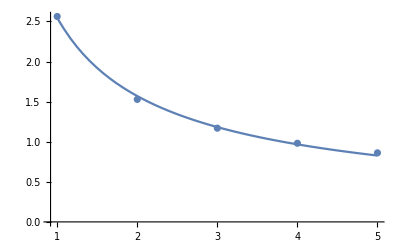

```mathematica
Show[ListPlot[{{1,f1[[1,2]]},{2,f2[[1,2]]},{3,f3[[1,2]]},{4,f4[[1,2]]},{5,f5[[1,2]]}}],Plot[fitU[x],{x,1,5}]]
```

```mathematica
Abs[fit2U[5,datatot5[nn+1][[p1,1]]]/datatot5[nn+1][[p1,4]]-1]100//Max
Abs[fit2U[4,datatot4[nn+1][[p2,1]]]/datatot4[nn+1][[p2,4]]-1]100//Max
Abs[fit2U[3,datatot3[nn+1][[p3,1]]]/datatot3[nn+1][[p3,4]]-1]100//Max
Abs[fit2U[2,datatot2[nn+1][[p4,1]]]/datatot2[nn+1][[p4,4]]-1]100//Max
Abs[fit2U[1,datatot[nn+1][[p5,1]]]/datatot[nn+1][[p5,4]]-1]100//Max
```

0.263856

0.0885523

0.215882

0.438752

0.154317

## ISCO

#### Hernquist

```mathematica
nn=30;
```

```mathematica
masses=Range[2,6,(6-2)/nn];
ISHQa0d7={10^#/10^7,background["HQ",10^#,10^7,10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[1,5,(5-1)/nn];
ISHQa0d6={10^#/10^6,background["HQ",10^#,10^6,10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[0,4,(4-0)/nn];
ISHQa0d5={10^#/10^5,background["HQ",10^#,10^5,10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[-1,3,(3-(-1))/nn];
ISHQa0d4={10^#/10^4,background["HQ",10^#,10^4,10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[-2,2,(2-(-2))/nn];
ISHQa0d3={10^#/10^3,background["HQ",10^#,10^3,10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[-3,1,(1-(-3))/nn];
ISHQa0d2={10^#/10^2,background["HQ",10^#,10^2,10^13][[2,4]]}&/@masses;
```

```mathematica
Export["./data/IS_HQ.mx",{ISHQa0d2,ISHQa0d3,ISHQa0d4,ISHQa0d5,ISHQa0d6,ISHQa0d7}]
```

./data/IS_HQ.mx

```mathematica
{ISHQa0d2,ISHQa0d3,ISHQa0d4,ISHQa0d5,ISHQa0d6,ISHQa0d7}=Import["./data/IS_HQ.mx"];
```

```mathematica
datatot[n_]:=Join[
Thread[{ISHQa0d7[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn][[1;;n]],(6Sqrt[6])ISHQa0d7[[1;;n,2]]}],
Thread[{ISHQa0d6[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn][[1;;n]],(6Sqrt[6])ISHQa0d6[[1;;n,2]]}],
Thread[{ISHQa0d5[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn][[1;;n]],(6Sqrt[6])ISHQa0d5[[1;;n,2]]}],Thread[{ISHQa0d4[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn][[1;;n]],(6Sqrt[6])ISHQa0d4[[1;;n,2]]}],Thread[{ISHQa0d3[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn][[1;;n]],(6Sqrt[6])ISHQa0d3[[1;;n,2]]}],Thread[{ISHQa0d2[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn][[1;;n]],(6Sqrt[6])ISHQa0d2[[1;;n,2]]}]];
```

```mathematica
pos=Intersection[Flatten[Position[N[datatot[nn+1][[All,1]]],xx_ /; xx<0.01]],Flatten[Position[N[datatot[nn+1][[All,3]]],xx_ /; xx>1]]];
fit1[x_,z_]=1-α x/z+β x^2/z^2+γ x/z^2//.FindFit[datatot[nn+1][[pos,2;;-1]],1-α x/z+β x^2/z^2+γ x/z^2,{α,β,γ},{z,x}]

fit2[x_,z_]=1-α x/z+β x^2/z^2+γ x/z^2//.FindFit[datatot[nn+1][[pos,2;;-1]],1-α x/z,{α,β,γ},{z,x}]
```

1+(64.4973486860681833006033 x)/z^2+(0.152910934690924456320366 x^2)/z^2-(0.999882912042288173934015 x)/z

1-(0.984684693927023411825874 x)/z

```mathematica
Abs[fit2[datatot[nn+1][[pos,3]],datatot[nn+1][[pos,2]]]/datatot[nn+1][[pos,4]]-1]100//Max
```

0.043661236453481336187

```mathematica
dataHQ={
Thread[{ISHQa0d7[[1;;nn+1,1]],(6Sqrt[6])ISHQa0d7[[1;;nn+1,2]]}],
Thread[{ISHQa0d6[[1;;nn+1,1]],(6Sqrt[6])ISHQa0d6[[1;;nn+1,2]]}],
Thread[{ISHQa0d5[[1;;nn+1,1]],(6Sqrt[6])ISHQa0d5[[1;;nn+1,2]]}],
Thread[{ISHQa0d4[[1;;nn+1,1]],(6Sqrt[6])ISHQa0d4[[1;;nn+1,2]]}],
Thread[{ISHQa0d3[[1;;nn+1,1]],(6Sqrt[6])ISHQa0d3[[1;;nn+1,2]]}]};
```

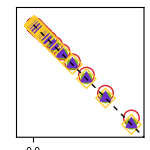

```mathematica
xl=Join[Table[{0.9984+0.0004i/5,,{0.012,0}},{i,0,100}],Table[{0.9984+0.0004i,Integerise[0.9984+0.0004i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9984+0.0004i/5,,{0.012,0}},{i,0,100}],Table[{0.9984+0.0004i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,Integerise[0.0005i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,,{0.02,0}},{i,0,100}]];

inset=Show[ListPlot[{dataHQ[[-1]],dataHQ[[-2]],dataHQ[[-3]],dataHQ[[-4]]},PlotMarkers->{{"○",16},{"●",12},{"▲",16},{"◇",20}},PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]},PlotRange->{{-0.0002,0.0015},{0.9985,1.0002}},Frame->True,Axes->False,FrameStyle->Directive[10,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],AspectRatio->1,ImageSize->150,ImagePadding->{{35, 15}, {20, 10}},FrameTicks->{{xl,xr},{xb,xu}}],Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]}]]
```

```mathematica
{0.01,0.02,0.04,0.06,0.08,0.1} 10^4
```

{100.,200.,400.,600.,800.,1000.}

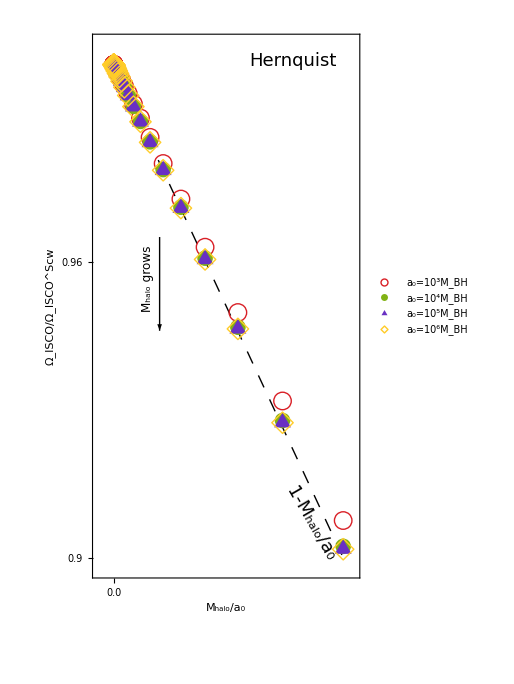

```mathematica
xl=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,Rotate[Integerise[0.9+0.02i],45Degree],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,Integerise[0.02i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,,{0.02,0}},{i,0,100}]];

xu2=Table[{{0.01,0.02,0.04,0.06,0.08,0.1}[[i]],Style[ToString[{"100","200","400","600","800","1000"}[[i]]],13],{0.02,0}},{i,1,6}];

p1=Show[Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{Style["Ω_ISCO/Ω_ISCO^Scw",22],None},{Style["M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["Hernquist",18,0,0.75,0.95,Black],leg["M_halo grows",12,90,0.205,0.55,Black],Inset[inset,Scaled[{0.68,0.78}]],leg["1-M_halo/a_0",18,-60,0.82,0.1,Black]},Axes->False,
FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-0.007,0.105},{0.898,1.004}}],
ListPlot[{dataHQ[[-1]],dataHQ[[-2]],dataHQ[[-3]],dataHQ[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",14],Style["a_0=10^4M_BH",14],Style["a_0=10^5M_BH",14],Style["a_0=10^6M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}],Graphics[Arrow[{{0.02,0.965},{0.02,0.946}}]]]
```

```mathematica
dataHQ={
Thread[{Log10[ISHQa0d7[[1;;nn+1,1]]],(6Sqrt[6])ISHQa0d7[[1;;nn+1,2]]}],
Thread[{Log10[ISHQa0d6[[1;;nn+1,1]]],(6Sqrt[6])ISHQa0d6[[1;;nn+1,2]]}],
Thread[{Log10[ISHQa0d5[[1;;nn+1,1]]],(6Sqrt[6])ISHQa0d5[[1;;nn+1,2]]}],
Thread[{Log10[ISHQa0d4[[1;;nn+1,1]]],(6Sqrt[6])ISHQa0d4[[1;;nn+1,2]]}],
Thread[{Log10[ISHQa0d3[[1;;nn+1,1]]],(6Sqrt[6])ISHQa0d3[[1;;nn+1,2]]}]};
```

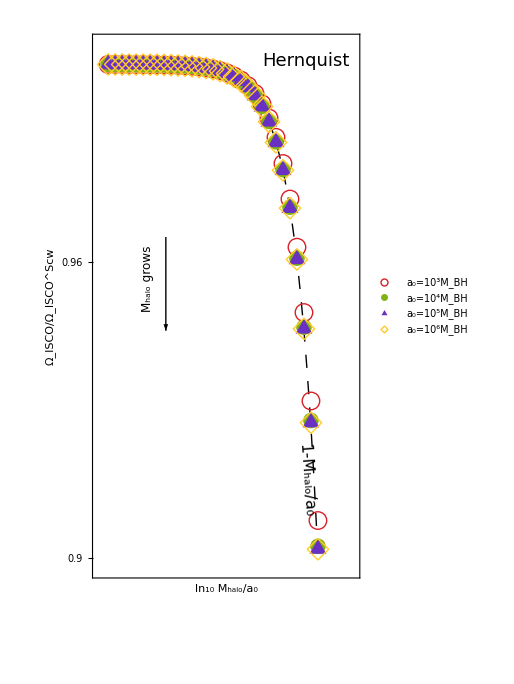

```mathematica
xl=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,Rotate[Integerise[0.9+0.02i],45Degree],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,Integerise[-6+1i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,,{0.02,0}},{i,0,100}]];

xu2=Table[{Log10[{0.0001,0.001,0.01,0.1}][[i]],Style[ToString[{"10","100","1000","1000"}[[i]]],13],{0.02,0}},{i,1,4}];

p1bis=Show[Plot[{1-10^z},{z,Log10[10^-5],Log10[10^-1]},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{Style["Ω_ISCO/Ω_ISCO^Scw",22],None},{Style["ln_10 M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["Hernquist",18,0,0.8,0.95,Black],leg["M_halo grows",12,90,0.205,0.55,Black],Inset[inset,Scaled[{0.3,0.78}]],leg["1-M_halo/a_0",16,-86,0.8,0.18,Black]},Axes->False,
FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-5.2,-0.3},{0.898,1.004}}],
ListPlot[{dataHQ[[-1]],dataHQ[[-2]],dataHQ[[-3]],dataHQ[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",14],Style["a_0=10^4M_BH",14],Style["a_0=10^5M_BH",14],Style["a_0=10^6M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}],Graphics[Arrow[{{-3.9,0.965},{-3.9,0.946}}]]]
```

#### NFW

```mathematica
nn=30;
```

```mathematica
masses=Range[2,6,(6-2)/nn];
ISNFWa0d7={10^#/10^7,background["NFW",10^#,{10^7,10^7},10^13][[2,4]]}&/@masses;
ISNFWa0d7v2={10^#/10^7,background["NFW",10^#,{10^7,2 10^7},10^13][[2,4]]}&/@masses;
ISNFWa0d7v3={10^#/10^7,background["NFW",10^#,{10^7,3 10^7},10^13][[2,4]]}&/@masses;
ISNFWa0d7v4={10^#/10^7,background["NFW",10^#,{10^7,4 10^7},10^13][[2,4]]}&/@masses;
ISNFWa0d7v5={10^#/10^7,background["NFW",10^#,{10^7,5 10^7},10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[1,5,(5-1)/nn];
ISNFWa0d6={10^#/10^6,background["NFW",10^#,{10^6,10^6},10^13][[2,4]]}&/@masses;
ISNFWa0d6v2={10^#/10^6,background["NFW",10^#,{10^6,2 10^6},10^13][[2,4]]}&/@masses;
ISNFWa0d6v3={10^#/10^6,background["NFW",10^#,{10^6,3 10^6},10^13][[2,4]]}&/@masses;
ISNFWa0d6v4={10^#/10^6,background["NFW",10^#,{10^6,4 10^6},10^13][[2,4]]}&/@masses;
ISNFWa0d6v5={10^#/10^6,background["NFW",10^#,{10^6,5 10^6},10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[0,4,(4-0)/nn];
ISNFWa0d5={10^#/10^5,background["NFW",10^#,{10^5,10^5},10^13][[2,4]]}&/@masses;
ISNFWa0d5v2={10^#/10^5,background["NFW",10^#,{10^5,2 10^5},10^13][[2,4]]}&/@masses;
ISNFWa0d5v3={10^#/10^5,background["NFW",10^#,{10^5,3 10^5},10^13][[2,4]]}&/@masses;ISNFWa0d5v4={10^#/10^5,background["NFW",10^#,{10^5,4 10^5},10^13][[2,4]]}&/@masses;
ISNFWa0d5v5={10^#/10^5,background["NFW",10^#,{10^5,5 10^5},10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[-1,3,(3-(-1))/nn];
ISNFWa0d4={10^#/10^4,background["NFW",10^#,{10^4,10^4},10^13][[2,4]]}&/@masses;
ISNFWa0d4v2={10^#/10^4,background["NFW",10^#,{10^4,2 10^4},10^13][[2,4]]}&/@masses;
ISNFWa0d4v3={10^#/10^4,background["NFW",10^#,{10^4,3 10^4},10^13][[2,4]]}&/@masses;
ISNFWa0d4v4={10^#/10^4,background["NFW",10^#,{10^4,4 10^4},10^13][[2,4]]}&/@masses;
ISNFWa0d4v5={10^#/10^4,background["NFW",10^#,{10^4,5 10^4},10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[-2,2,(2-(-2))/nn];
ISNFWa0d3={10^#/10^3,background["NFW",10^#,{10^3,10^3},10^13][[2,4]]}&/@masses;
ISNFWa0d3v2={10^#/10^3,background["NFW",10^#,{10^3,2 10^3},10^13][[2,4]]}&/@masses;
ISNFWa0d3v3={10^#/10^3,background["NFW",10^#,{10^3,3 10^3},10^13][[2,4]]}&/@masses;
ISNFWa0d3v4={10^#/10^3,background["NFW",10^#,{10^3,4 10^3},10^13][[2,4]]}&/@masses;
ISNFWa0d3v5={10^#/10^3,background["NFW",10^#,{10^3,5 10^3},10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[-3,1,(1-(-3))/nn];
ISNFWa0d2={10^#/10^2,background["NFW",10^#,{10^2,10^2},10^13][[2,4]]}&/@masses;
ISNFWa0d2v2={10^#/10^2,background["NFW",10^#,{10^2,2 10^2},10^13][[2,4]]}&/@masses;
ISNFWa0d2v3={10^#/10^2,background["NFW",10^#,{10^2,3 10^2},10^13][[2,4]]}&/@masses;
ISNFWa0d2v4={10^#/10^2,background["NFW",10^#,{10^2,4 10^2},10^13][[2,4]]}&/@masses;
ISNFWa0d2v5={10^#/10^2,background["NFW",10^#,{10^2,5 10^2},10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[-4,0,(0-(-4))/nn];
ISNFWa0d1={10^#/10,background["NFW",10^#,{10,10},10^13][[2,4]]}&/@masses;
ISNFWa0d1v2={10^#/10,background["NFW",10^#,{10,2 10},10^13][[2,4]]}&/@masses;
ISNFWa0d1v3={10^#/10,background["NFW",10^#,{10,3 10},10^13][[2,4]]}&/@masses;
ISNFWa0d1v4={10^#/10,background["NFW",10^#,{10,4 10},10^13][[2,4]]}&/@masses;
ISNFWa0d1v5={10^#/10,background["NFW",10^#,{10,5 10},10^13][[2,4]]}&/@masses;
```

```mathematica
Export["./data/IS_NFW.mx",
{{ISNFWa0d7,ISNFWa0d6,ISNFWa0d5,ISNFWa0d4,ISNFWa0d3,ISNFWa0d2,ISNFWa0d1},
{ISNFWa0d7v2,ISNFWa0d6v2,ISNFWa0d5v2,ISNFWa0d4v2,ISNFWa0d3v2,ISNFWa0d2v2,ISNFWa0d1v2},
{ISNFWa0d7v3,ISNFWa0d6v3,ISNFWa0d5v3,ISNFWa0d4v3,ISNFWa0d3v3,ISNFWa0d2v3,ISNFWa0d1v3},{ISNFWa0d7v4,ISNFWa0d6v4,ISNFWa0d5v4,ISNFWa0d4v4,ISNFWa0d3v4,ISNFWa0d2v4,ISNFWa0d1v4},
{ISNFWa0d7v5,ISNFWa0d6v5,ISNFWa0d5v5,ISNFWa0d4v5,ISNFWa0d3v5,ISNFWa0d2v5,ISNFWa0d1v5}}]
```

./data/IS_NFW.mx

```mathematica
{{ISNFWa0d7,ISNFWa0d6,ISNFWa0d5,ISNFWa0d4,ISNFWa0d3,ISNFWa0d2,ISNFWa0d1},
{ISNFWa0d7v2,ISNFWa0d6v2,ISNFWa0d5v2,ISNFWa0d4v2,ISNFWa0d3v2,ISNFWa0d2v2,ISNFWa0d1v2},
{ISNFWa0d7v3,ISNFWa0d6v3,ISNFWa0d5v3,ISNFWa0d4v3,ISNFWa0d3v3,ISNFWa0d2v3,ISNFWa0d1v3},{ISNFWa0d7v4,ISNFWa0d6v4,ISNFWa0d5v4,ISNFWa0d4v4,ISNFWa0d3v4,ISNFWa0d2v4,ISNFWa0d1v4},
{ISNFWa0d7v5,ISNFWa0d6v5,ISNFWa0d5v5,ISNFWa0d4v5,ISNFWa0d3v5,ISNFWa0d2v5,ISNFWa0d1v5}}=Import["./data/IS_NFW.mx"];
```

```mathematica
dataNFW={
Thread[{ISNFWa0d7[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d7[[1;;nn+1,2]]}],
Thread[{ISNFWa0d6[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d6[[1;;nn+1,2]]}],
Thread[{ISNFWa0d5[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d5[[1;;nn+1,2]]}],
Thread[{ISNFWa0d4[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d4[[1;;nn+1,2]]}],
Thread[{ISNFWa0d3[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d3[[1;;nn+1,2]]}]};

dataNFWv2={
Thread[{ISNFWa0d7v2[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d7v2[[1;;nn+1,2]]}],
Thread[{ISNFWa0d6v2[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d6v2[[1;;nn+1,2]]}],
Thread[{ISNFWa0d5v2[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d5v2[[1;;nn+1,2]]}],
Thread[{ISNFWa0d4v2[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d4v2[[1;;nn+1,2]]}],
Thread[{ISNFWa0d3v2[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d3v2[[1;;nn+1,2]]}]};

dataNFWv5={
Thread[{ISNFWa0d7v5[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d7v5[[1;;nn+1,2]]}],
Thread[{ISNFWa0d6v5[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d6v5[[1;;nn+1,2]]}],
Thread[{ISNFWa0d5v5[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d5v5[[1;;nn+1,2]]}],
Thread[{ISNFWa0d4v5[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d4v5[[1;;nn+1,2]]}],
Thread[{ISNFWa0d3v5[[1;;nn+1,1]],(6Sqrt[6])ISNFWa0d3v5[[1;;nn+1,2]]}]};
```

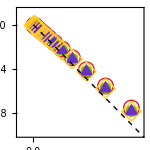

```mathematica
xl=Join[Table[{0.9984+0.0004i/5,,{0.012,0}},{i,0,100}],Table[{0.9984+0.0004i,Integerise[0.9984+0.0004i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9984+0.0004i/5,,{0.012,0}},{i,0,100}],Table[{0.9984+0.0004i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,Integerise[0.0005i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,,{0.02,0}},{i,0,100}]];

xu2=Table[{{0.01,0.02,0.04,0.06,0.08,0.1}[[i]],Style[ToString[{"100","200","400","600","800","1000"}[[i]]],13],{0.02,0}},{i,1,6}];

inset2=Show[ListPlot[{dataNFWv5[[-1]],dataNFWv5[[-2]],dataNFWv5[[-3]],dataNFWv5[[-4]]},PlotMarkers->{{"○",16},{"●",12},{"▲",16},{"◇",20}},PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]},PlotRange->{{-0.0002,0.0015},{0.9985,1.0002}},Frame->True,Axes->False,FrameStyle->Directive[10,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],AspectRatio->1,ImageSize->150,ImagePadding->{{10, 35}, {20, 10}},FrameTicks->{{xr,xl},{xb,xu}}],Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]}]]
```

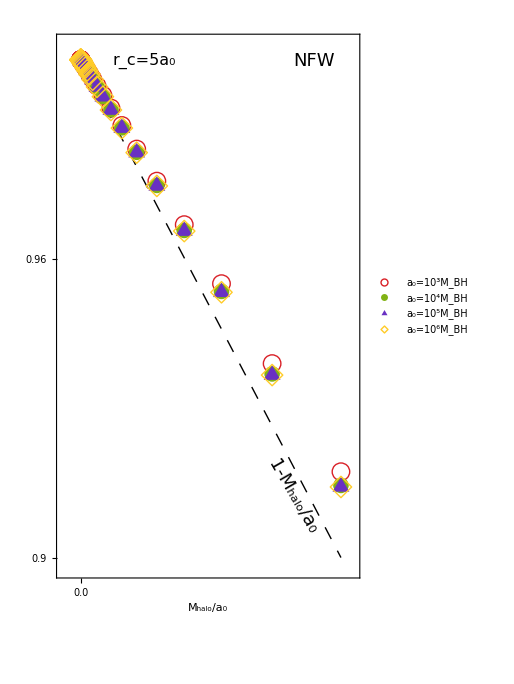

```mathematica
xl=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,Rotate[Integerise[0.9+0.02i],45Degree],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,Integerise[0.02i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,,{0.02,0}},{i,0,100}]];

xu2=Table[{{0.01,0.02,0.04,0.06,0.08,0.1}[[i]],Style[ToString[{"100","200","400","600","800","1000"}[[i]]],13],{0.02,0}},{i,1,6}];

p2=Show[Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{None,None},{Style["M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",18,-60,0.78,0.15,Black],leg["NFW",18,0,0.85,0.95,Black],leg["r_c=5a_0",16,0,0.29,0.95,Black],Inset[inset2,Scaled[{0.72,0.78}]]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-0.007,0.105},{0.898,1.003}}],
ListPlot[{dataNFWv5[[-1]],dataNFWv5[[-2]],dataNFWv5[[-3]],dataNFWv5[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",14],Style["a_0=10^4M_BH",14],Style["a_0=10^5M_BH",14],Style["a_0=10^6M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

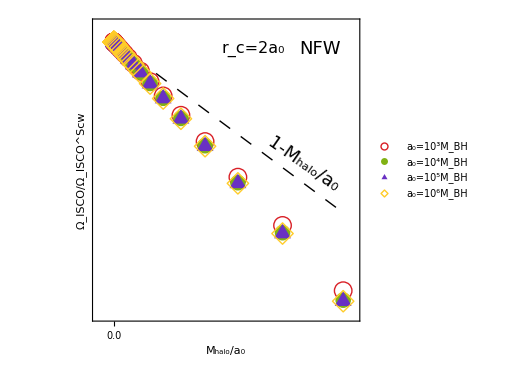

```mathematica
xl=Join[Table[{0.82+0.04i/5,,{0.012,0}},{i,0,100}],Table[{0.82+0.04i,Integerise[0.82+0.04i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.82+0.04i/5,,{0.012,0}},{i,0,100}],Table[{0.82+0.04i,,{0.02,0}},{i,0,100}]];

p22=Show[Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{Style["Ω_ISCO/Ω_ISCO^Scw",22],None},{Style["M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",18,-35,0.79,0.52,Black],leg["NFW",18,0,0.85,0.9,Black],leg["r_c=2a_0",16,0,0.6,0.9,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-0.007,0.105},{0.84,1.01}}],
ListPlot[{dataNFWv2[[-1]],dataNFWv2[[-2]],dataNFWv2[[-3]],dataNFWv2[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",12],Style["a_0=10^4M_BH",12],Style["a_0=10^5M_BH",12],Style["a_0=10^6M_BH",12]},Scaled[{0.22,0.22}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

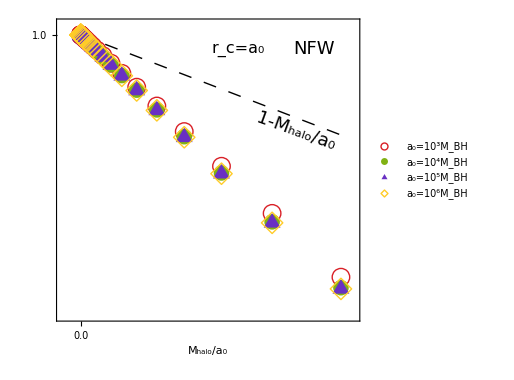

```mathematica
xl=Join[Table[{0.7+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.7+0.05i,Integerise[0.7+0.05i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.7+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.7+0.05i,,{0.02,0}},{i,0,100}]];

p23=Show[Plot[{1-z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{None,None},{Style["M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",18,-20,0.79,0.63,Black],leg["NFW",18,0,0.85,0.9,Black],leg["r_c=a_0",16,0,0.6,0.9,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-0.007,0.105},{0.72,1.01}}],
ListPlot[{dataNFW[[-1]],dataNFW[[-2]],dataNFW[[-3]],dataNFW[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",12],Style["a_0=10^4M_BH",12],Style["a_0=10^5M_BH",12],Style["a_0=10^6M_BH",12]},Scaled[{0.22,0.22}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

```mathematica
dataNFW={
Thread[{Log10[ISNFWa0d7[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d7[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d6[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d6[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d5[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d5[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d4[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d4[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d3[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d3[[1;;nn+1,2]]}]};

dataNFWv2={
Thread[{Log10[ISNFWa0d7v2[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d7v2[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d6v2[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d6v2[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d5v2[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d5v2[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d4v2[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d4v2[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d3v2[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d3v2[[1;;nn+1,2]]}]};

dataNFWv5={
Thread[{Log10[ISNFWa0d7v5[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d7v5[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d6v5[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d6v5[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d5v5[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d5v5[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d4v5[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d4v5[[1;;nn+1,2]]}],
Thread[{Log10[ISNFWa0d3v5[[1;;nn+1,1]]],(6Sqrt[6])ISNFWa0d3v5[[1;;nn+1,2]]}]};
```

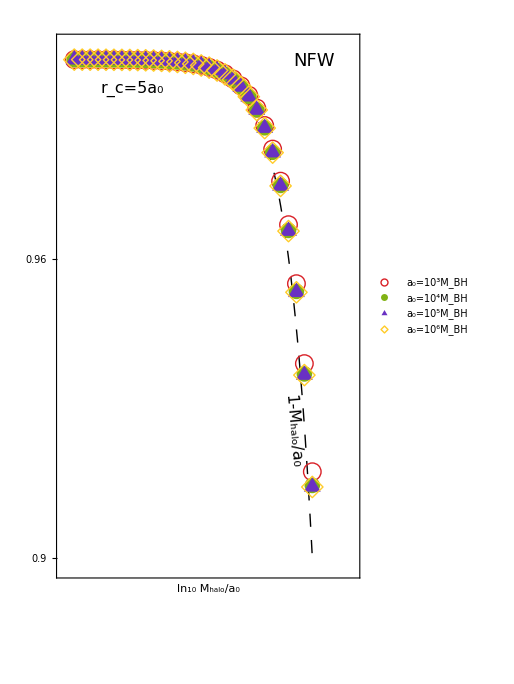

```mathematica
xl=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,Rotate[Integerise[0.9+0.02i],45Degree],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.9+0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.9+0.02i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,Integerise[-6+1i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,,{0.02,0}},{i,0,100}]];

xu2=Table[{Log10[{0.0001,0.001,0.01,0.1}][[i]],Style[ToString[{"10","100","1000","1000"}[[i]]],13],{0.02,0}},{i,1,4}];

p2bis=Show[Plot[{1-10^z},{z,Log10[10^-5],Log10[0.1]},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{None,None},{Style["ln_10 M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",16,-85,0.78,0.27,Black],leg["NFW",18,0,0.85,0.95,Black],leg["r_c=5a_0",16,0,0.25,0.9,Black],Inset[inset2,Scaled[{0.3,0.7}]]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-5.2,-0.3},{0.898,1.003}}],
ListPlot[{dataNFWv5[[-1]],dataNFWv5[[-2]],dataNFWv5[[-3]],dataNFWv5[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",14],Style["a_0=10^4M_BH",14],Style["a_0=10^5M_BH",14],Style["a_0=10^6M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

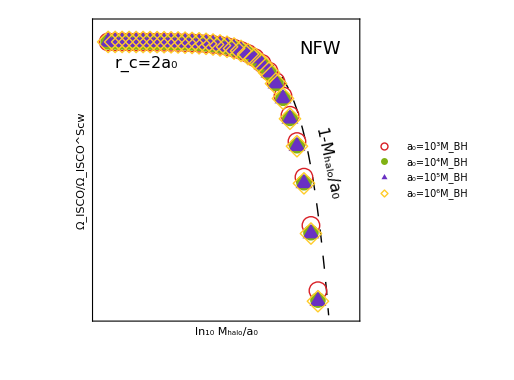

```mathematica
xl=Join[Table[{0.82+0.04i/5,,{0.012,0}},{i,0,100}],Table[{0.82+0.04i,Integerise[0.82+0.04i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.82+0.04i/5,,{0.012,0}},{i,0,100}],Table[{0.82+0.04i,,{0.02,0}},{i,0,100}]];

p22bis=Show[Plot[{1-10^z},{z,Log10[10^-5],Log10[0.2]},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{Style["Ω_ISCO/Ω_ISCO^Scw",22],None},{Style["ln_10 M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",16,-78,0.88,0.52,Black],leg["NFW",18,0,0.85,0.9,Black],leg["r_c=2a_0",16,0,0.2,0.85,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-5.2,-0.3},{0.84,1.01}}],
ListPlot[{dataNFWv2[[-1]],dataNFWv2[[-2]],dataNFWv2[[-3]],dataNFWv2[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",12],Style["a_0=10^4M_BH",12],Style["a_0=10^5M_BH",12],Style["a_0=10^6M_BH",12]},Scaled[{0.22,0.22}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

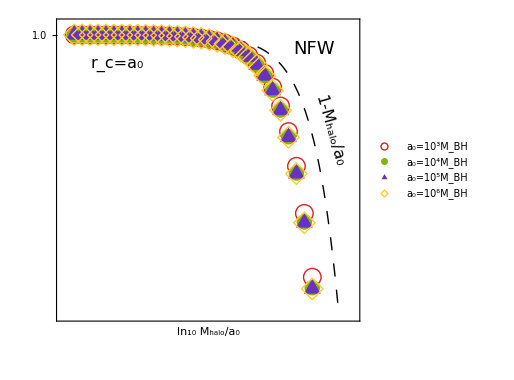

```mathematica
xl=Join[Table[{0.7+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.7+0.05i,Integerise[0.7+0.05i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.7+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.7+0.05i,,{0.02,0}},{i,0,100}]];

p23bis=Show[Plot[{1-10^z},{z,Log10[10^-5],Log10[0.3]},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,
FrameLabel->{{None,None},{Style["ln_10 M_halo/a_0",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1,ImagePadding->{{85, 10}, {55, 35}},Epilog->{leg["1-M_halo/a_0",16,-74,0.9,0.63,Black],leg["NFW",18,0,0.85,0.9,Black],leg["r_c=a_0",16,0,0.2,0.85,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-5.2,-0.3},{0.72,1.01}}],
ListPlot[{dataNFW[[-1]],dataNFW[[-2]],dataNFW[[-3]],dataNFW[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["a_0=10^3M_BH",12],Style["a_0=10^4M_BH",12],Style["a_0=10^5M_BH",12],Style["a_0=10^6M_BH",12]},Scaled[{0.22,0.22}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

#### Einasto

```mathematica
nn=30;
```

```mathematica
masses=Range[2,6,(6-2)/nn];
ISEina0d7={10^#/10^7,background["Ein",10^#,{10^7,10^13},10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[1,5,(5-1)/nn];
ISEina0d6={10^#/10^6,background["Ein",10^#,{10^6,10^13},10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[0,4,(4-0)/nn];
ISEina0d5={10^#/10^5,background["Ein",10^#,{10^5,10^13},10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[-1,3,(3-(-1))/nn];
ISEina0d4={10^#/10^4,background["Ein",10^#,{10^4,10^13},10^13][[2,4]]}&/@masses;
```

```mathematica
masses=Range[-2,2,(2-(-2))/nn];
ISEina0d3={10^#/10^3,background["Ein",10^#,{10^3,10^13},10^13][[2,4]]}&/@masses;
```

```mathematica
Export["./data/IS_Ein.mx",{ISEina0d7,ISEina0d6,ISEina0d5,ISEina0d4,ISEina0d3}]
```

./data/IS_Ein.mx

```mathematica
{ISEina0d7,ISEina0d6,ISEina0d5,ISEina0d4,ISEina0d3}=Import["./data/IS_Ein.mx"];
```

```mathematica
dataEin={
Thread[{ISEina0d7[[All,1]],(6Sqrt[6])ISEina0d7[[All,2]]}],
Thread[{ISEina0d6[[All,1]],(6Sqrt[6])ISEina0d6[[All,2]]}],
Thread[{ISEina0d5[[All,1]],(6Sqrt[6])ISEina0d5[[All,2]]}],
Thread[{ISEina0d4[[All,1]],(6Sqrt[6])ISEina0d4[[All,2]]}],
Thread[{ISEina0d3[[All,1]],(6Sqrt[6])ISEina0d3[[All,2]]}]};
```

```mathematica
FindFit[Partition[Flatten[dataEin],2],a+b xx,{a,b,c},xx];
fitEin[xx_]=a+b xx//.%
```

0.999579670338165926832003-2.98278101073562880184122 xx

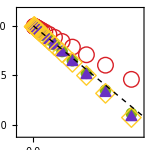

```mathematica
xl=Join[Table[{0.95+0.002i/5,,{0.012,0}},{i,0,1000}],Table[{0.95+0.002i,Integerise[0.95+0.002i],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.95+0.002i/5,,{0.012,0}},{i,0,1000}],Table[{0.95+0.002i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,Integerise[0.0005i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.0005i/5,,{0.012,0}},{i,0,100}],Table[{0.0005i,,{0.02,0}},{i,0,100}]];

inset3=Show[ListPlot[{dataEin[[-1]],dataEin[[-2]],dataEin[[-3]],dataEin[[-4]]},PlotMarkers->{{"○",16},{"●",12},{"▲",16},{"◇",20}},PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]},PlotRange->{{-0.0002,0.0015},{0.9945,1.0008}},Frame->True,Axes->False,FrameStyle->Directive[10,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],AspectRatio->1,ImageSize->150,ImagePadding->{{10, 35}, {20, 10}},FrameTicks->{{xr,xl},{xb,xu}}],Plot[{1-3z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]}]]
```

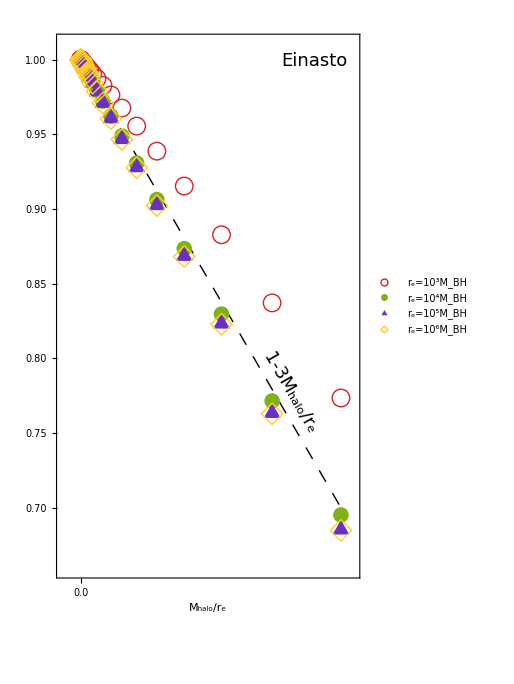

```mathematica
xl=Join[Table[{0.5+0.05i/5,,{0.012,0}},{i,0,200}],Table[{0.5+0.05i,Rotate[Integerise[0.5+0.05i],45Degree],{0.02,0}},{i,0,100}]];
xr=Join[Table[{0.5+0.05i/5,,{0.012,0}},{i,0,100}],Table[{0.5+0.05i,,{0.02,0}},{i,0,100}]];

xb=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,Integerise[0.02i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.02i/5,,{0.012,0}},{i,0,100}],Table[{0.02i,,{0.02,0}},{i,0,100}]];

xu2=Table[{{0.01,0.02,0.04,0.06,0.08,0.1}[[i]],Style[ToString[{"100","200","400","600","800","1000"}[[i]]],13],{0.02,0}},{i,1,6}];

p3=Show[Plot[{1-3z},{z,0,0.1},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,FrameLabel->{{None,None},{Style["M_halo/r_e",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{Inset[inset3,Scaled[{0.26,0.38}]],leg["1-3M_halo/r_e",18,-60,0.77,0.34,Black],leg["Einasto",18,0,0.85,0.95,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-0.007,0.105},{0.66,1.01}}],
ListPlot[{dataEin[[-1]],dataEin[[-2]],dataEin[[-3]],dataEin[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["r_e=10^3M_BH",14],Style["r_e=10^4M_BH",14],Style["r_e=10^5M_BH",14],Style["r_e=10^6M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

```mathematica
dataEin={
Thread[{Log10[ISEina0d7[[All,1]]],(6Sqrt[6])ISEina0d7[[All,2]]}],
Thread[{Log10[ISEina0d6[[All,1]]],(6Sqrt[6])ISEina0d6[[All,2]]}],
Thread[{Log10[ISEina0d5[[All,1]]],(6Sqrt[6])ISEina0d5[[All,2]]}],
Thread[{Log10[ISEina0d4[[All,1]]],(6Sqrt[6])ISEina0d4[[All,2]]}],
Thread[{Log10[ISEina0d3[[All,1]]],(6Sqrt[6])ISEina0d3[[All,2]]}]};
```

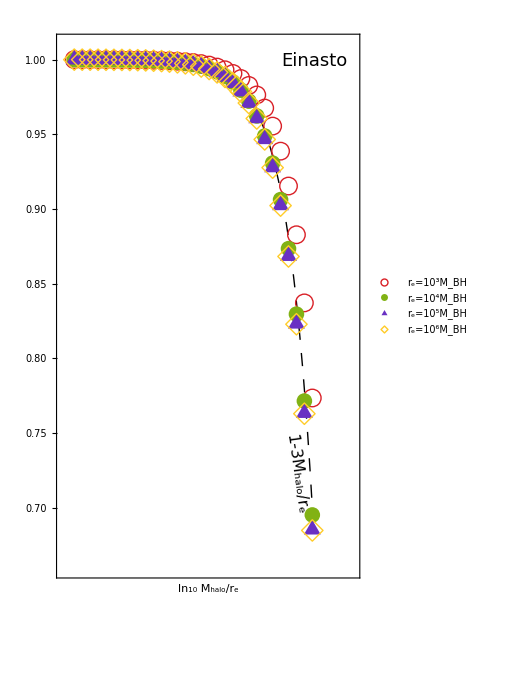

```mathematica
xb=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,Integerise[-6+1i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{-6+1i/5,,{0.012,0}},{i,0,100}],Table[{-6+1i,,{0.02,0}},{i,0,100}]];

xu2=Table[{Log10[{0.0001,0.001,0.01,0.1}][[i]],Style[ToString[{"10","100","1000","1000"}[[i]]],13],{0.02,0}},{i,1,4}];

p3bis=Show[Plot[{1-3 10^z},{z,Log10[10^-5],Log10[10^-1]},
PlotStyle->{Directive[Black,Dashing[{0.025,0.025}],AbsoluteThickness[1]]},
Frame->True,FrameLabel->{{None,None},{Style["ln_10 M_halo/r_e",22],None}},
ImageSize->380,
FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1.2]],AspectRatio->1.8,ImagePadding->{{85, 10}, {55, 35}},Epilog->{Inset[inset3,Scaled[{0.3,0.75}]],leg["1-3M_halo/r_e",16,-82,0.79,0.19,Black],leg["Einasto",18,0,0.85,0.95,Black]},Axes->False,FrameTicks->{{xl,xr},{xb,xu2}},PlotRange->{{-5.2,-0.3},{0.66,1.01}}],
ListPlot[{dataEin[[-1]],dataEin[[-2]],dataEin[[-3]],dataEin[[-4]]},PlotMarkers->{{"○",18},{"●",16},{"▲",20},{"◇",22}},PlotLegends->Placed[{Style["r_e=10^3M_BH",14],Style["r_e=10^4M_BH",14],Style["r_e=10^5M_BH",14],Style["r_e=10^6M_BH",14]},Scaled[{0.22,0.13}]],PlotStyle->{Comb2[[1]],Comb1[[2]],Comb3[[2]],Comb1[[3]]}]]
```

#### Final grouping

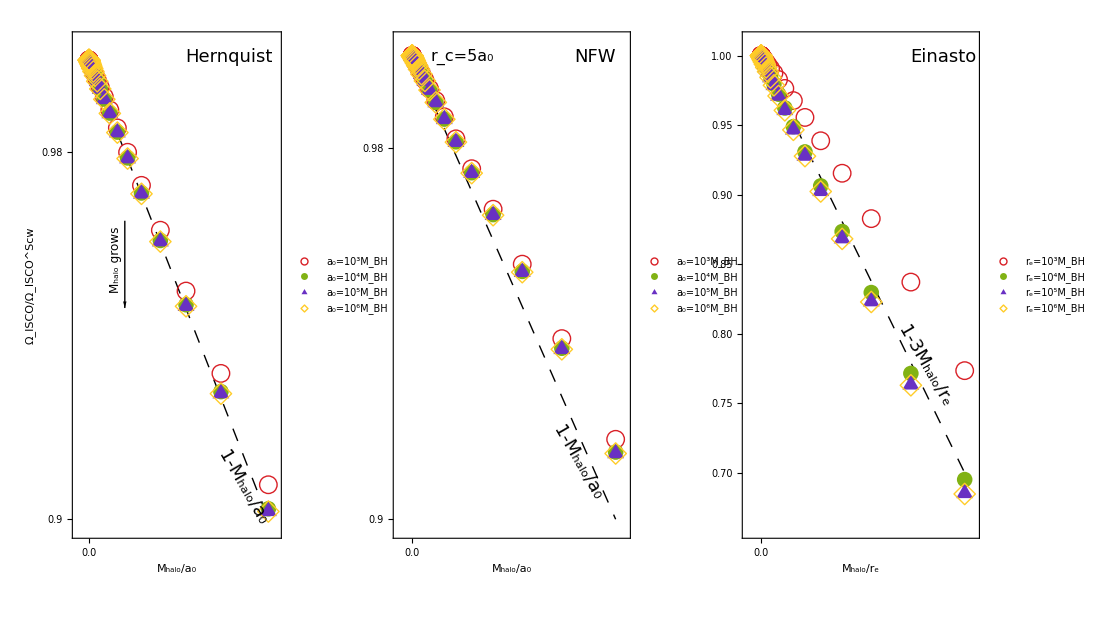

./plot/Fig3b.pdf

```mathematica
GraphicsRow[{p1,p2,p3},ImageSize->1100,Spacings->-50,ImagePadding->{{20,60}, {0, 0}}]
Export["./plot/Fig3b.pdf",%]
```

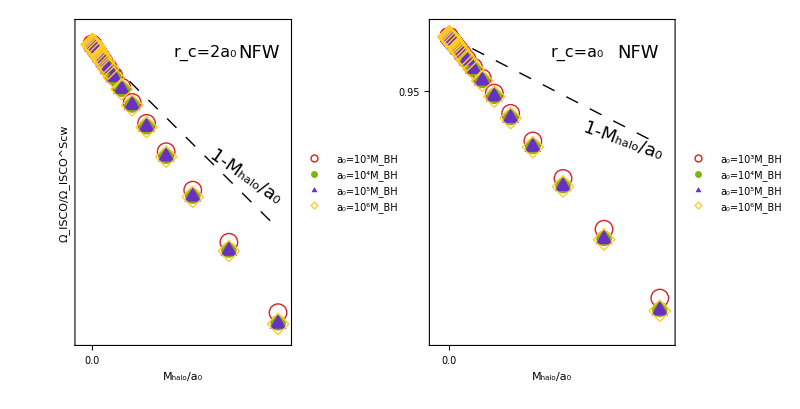

./plot/Fig4b.pdf

```mathematica
GraphicsRow[{p22,p23},ImageSize->800,Spacings->-30,ImagePadding->{{20,60}, {0, 0}}]
Export["./plot/Fig4b.pdf",%]
```

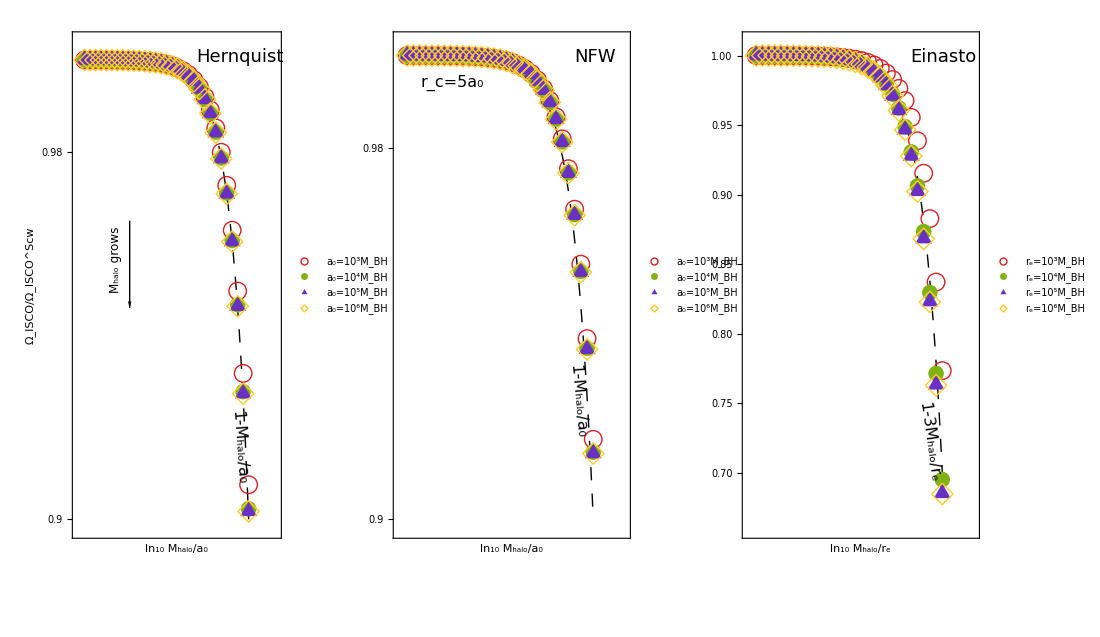

./plot/Fig3bbis.pdf

```mathematica
GraphicsRow[{p1bis,p2bis,p3bis},ImageSize->1100,Spacings->-50,ImagePadding->{{20,60}, {0, 0}}]
Export["./plot/Fig3bbis.pdf",%]
```

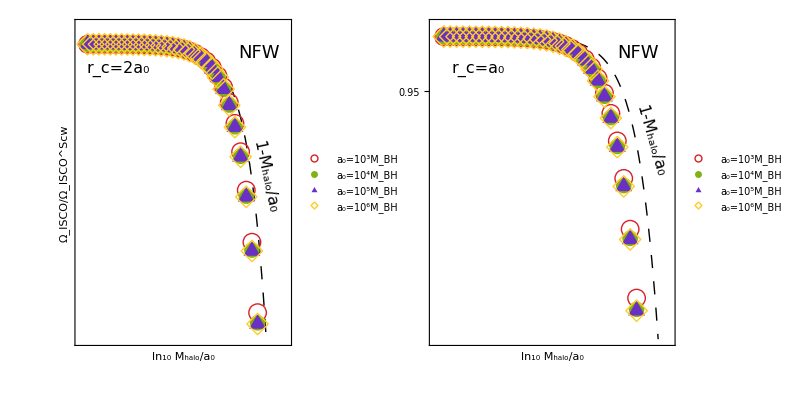

./plot/Fig4bbis.pdf

```mathematica
GraphicsRow[{p22bis,p23bis},ImageSize->800,Spacings->-30,ImagePadding->{{20,60}, {0, 0}}]
Export["./plot/Fig4bbis.pdf",%]
```

#### Fit for NFW

```mathematica
{{ISNFWa0d7,ISNFWa0d6,ISNFWa0d5,ISNFWa0d4,ISNFWa0d3,ISNFWa0d2,ISNFWa0d1},
{ISNFWa0d7v2,ISNFWa0d6v2,ISNFWa0d5v2,ISNFWa0d4v2,ISNFWa0d3v2,ISNFWa0d2v2,ISNFWa0d1v2},
{ISNFWa0d7v3,ISNFWa0d6v3,ISNFWa0d5v3,ISNFWa0d4v3,ISNFWa0d3v3,ISNFWa0d2v3,ISNFWa0d1v3},{ISNFWa0d7v4,ISNFWa0d6v4,ISNFWa0d5v4,ISNFWa0d4v4,ISNFWa0d3v4,ISNFWa0d2v4,ISNFWa0d1v4},
{ISNFWa0d7v5,ISNFWa0d6v5,ISNFWa0d5v5,ISNFWa0d4v5,ISNFWa0d3v5,ISNFWa0d2v5,ISNFWa0d1v5}}=Import["./data/IS_NFW.mx"];
```

```mathematica
datatot[n_]:=Join[
Thread[{ISNFWa0d7[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn],(6Sqrt[6])ISNFWa0d7[[1;;n,2]]}],
Thread[{ISNFWa0d6[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn],(6Sqrt[6])ISNFWa0d6[[1;;n,2]]}],
Thread[{ISNFWa0d5[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(6Sqrt[6])ISNFWa0d5[[1;;n,2]]}],
Thread[{ISNFWa0d4[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(6Sqrt[6])ISNFWa0d4[[1;;n,2]]}],Thread[{ISNFWa0d3[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(6Sqrt[6])ISNFWa0d3[[1;;n,2]]}],Thread[{ISNFWa0d2[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(6Sqrt[6])ISNFWa0d2[[1;;n,2]]}]]//N
```

```mathematica
datatot2[n_]:=Join[
Thread[{ISNFWa0d7v2[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn],(6Sqrt[6])ISNFWa0d7v2[[1;;n,2]]}],
Thread[{ISNFWa0d6v2[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn],(6Sqrt[6])ISNFWa0d6v2[[1;;n,2]]}],
Thread[{ISNFWa0d5v2[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(6Sqrt[6])ISNFWa0d5v2[[1;;n,2]]}],
Thread[{ISNFWa0d4v2[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(6Sqrt[6])ISNFWa0d4v2[[1;;n,2]]}],Thread[{ISNFWa0d3v2[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(6Sqrt[6])ISNFWa0d3v2[[1;;n,2]]}],Thread[{ISNFWa0d2v2[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(6Sqrt[6])ISNFWa0d2v2[[1;;n,2]]}]]//N
```

```mathematica
datatot3[n_]:=Join[
Thread[{ISNFWa0d7v2[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn],(6Sqrt[6])ISNFWa0d7v3[[1;;n,2]]}],
Thread[{ISNFWa0d6v3[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn],(6Sqrt[6])ISNFWa0d6v3[[1;;n,2]]}],
Thread[{ISNFWa0d5v3[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(6Sqrt[6])ISNFWa0d5v3[[1;;n,2]]}],
Thread[{ISNFWa0d4v3[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(6Sqrt[6])ISNFWa0d4v3[[1;;n,2]]}],Thread[{ISNFWa0d3v3[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(6Sqrt[6])ISNFWa0d3v3[[1;;n,2]]}],Thread[{ISNFWa0d2v3[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(6Sqrt[6])ISNFWa0d2v3[[1;;n,2]]}]]//N
```

```mathematica
datatot4[n_]:=Join[
Thread[{ISNFWa0d7v4[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn],(6Sqrt[6])ISNFWa0d7v4[[1;;n,2]]}],
Thread[{ISNFWa0d6v4[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn],(6Sqrt[6])ISNFWa0d6v4[[1;;n,2]]}],
Thread[{ISNFWa0d5v4[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(6Sqrt[6])ISNFWa0d5v4[[1;;n,2]]}],
Thread[{ISNFWa0d4v4[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(6Sqrt[6])ISNFWa0d4v4[[1;;n,2]]}],Thread[{ISNFWa0d3v4[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(6Sqrt[6])ISNFWa0d3v4[[1;;n,2]]}],Thread[{ISNFWa0d2v4[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(6Sqrt[6])ISNFWa0d2v4[[1;;n,2]]}]]//N
```

```mathematica
datatot5[n_]:=Join[
Thread[{ISNFWa0d7v5[[1;;n,1]],ConstantArray[10^7,n],10^Range[2,6,(6-2)/nn],(6Sqrt[6])ISNFWa0d7v5[[1;;n,2]]}],
Thread[{ISNFWa0d6v5[[1;;n,1]],ConstantArray[10^6,n],10^Range[1,5,(5-1)/nn],(6Sqrt[6])ISNFWa0d6v5[[1;;n,2]]}],
Thread[{ISNFWa0d5v5[[1;;n,1]],ConstantArray[10^5,n],10^Range[0,4,(4-0)/nn],(6Sqrt[6])ISNFWa0d5v5[[1;;n,2]]}],
Thread[{ISNFWa0d4v5[[1;;n,1]],ConstantArray[10^4,n],10^Range[-1,3,(3-(-1))/nn],(6Sqrt[6])ISNFWa0d4v5[[1;;n,2]]}],Thread[{ISNFWa0d3v5[[1;;n,1]],ConstantArray[10^3,n],10^Range[-2,2,(2-(-2))/nn],(6Sqrt[6])ISNFWa0d3v5[[1;;n,2]]}],Thread[{ISNFWa0d2v5[[1;;n,1]],ConstantArray[10^2,n],10^Range[-3,1,(1-(-3))/nn],(6Sqrt[6])ISNFWa0d2v5[[1;;n,2]]}]]//N
```

```mathematica
climit=0.01;
```

```mathematica
p1=Intersection[Flatten[Position[N[datatot[nn+1][[All,1]]],xx_ /; xx<climit]],Flatten[Position[N[datatot[nn+1][[All,3]]],xx_ /; xx>1]]];
f1=FindFit[datatot[nn+1][[p1,2;;-1]],1-α x/z,{α,β,γ},{z,x}];
fit[x_,z_]=1-α x/z//.f1
Abs[fit[datatot[nn+1][[p1,3]],datatot[nn+1][[p1,2]]]/datatot[nn+1][[p1,4]]-1]//Max
```

1-(2.55073 x)/z

0.00108252

```mathematica
p2=Intersection[Flatten[Position[N[datatot2[nn+1][[All,1]]],xx_ /; xx<climit]],Flatten[Position[N[datatot2[nn+1][[All,3]]],xx_ /; xx>1]]];
f2=FindFit[datatot2[nn+1][[p2,2;;-1]],1-α x/z,{α,β,γ},{z,x}];
fit[x_,z_]=1-α x/z//.f2
Abs[fit[datatot2[nn+1][[p2,3]],datatot2[nn+1][[p2,2]]]/datatot2[nn+1][[p2,4]]-1]//Max
```

1-(1.52583 x)/z

0.000493183

```mathematica
p3=Intersection[Flatten[Position[N[datatot3[nn+1][[All,1]]],xx_ /; xx<climit]],Flatten[Position[N[datatot3[nn+1][[All,3]]],xx_ /; xx>1]]];
f3=FindFit[datatot3[nn+1][[p3,2;;-1]],1-α x/z,{α,β,γ},{z,x}];
fit[x_,z_]=1-α x/z//.f3
Abs[fit[datatot3[nn+1][[p3,3]],datatot3[nn+1][[p3,2]]]/datatot3[nn+1][[p3,4]]-1]//Max
```

1-(1.16662 x)/z

0.000337907

```mathematica
p4=Intersection[Flatten[Position[N[datatot4[nn+1][[All,1]]],xx_ /; xx<climit]],Flatten[Position[N[datatot4[nn+1][[All,3]]],xx_ /; xx>1]]];
f4=FindFit[datatot4[nn+1][[p4,2;;-1]],1-α x/z,{α,β,γ},{z,x}];
fit[x_,z_]=1-α x/z//.f4
Abs[fit[datatot4[nn+1][[p4,3]],datatot4[nn+1][[p4,2]]]/datatot4[nn+1][[p4,4]]-1]//Max
```

1-(0.978796 x)/z

0.000267135

```mathematica
p5=Intersection[Flatten[Position[N[datatot5[nn+1][[All,1]]],xx_ /; xx<climit]],Flatten[Position[N[datatot5[nn+1][[All,3]]],xx_ /; xx>1]]];
f5=FindFit[datatot5[nn+1][[p5,2;;-1]],1-α x/z,{α,β,γ},{z,x}];
fit[x_,z_]=1-α x/z//.f5
Abs[fit[datatot5[nn+1][[p5,3]],datatot5[nn+1][[p5,2]]]/datatot5[nn+1][[p5,4]]-1]//Max
```

1-(0.861399 x)/z

0.000226483

```mathematica
FindFit[{{1,f1[[1,2]]},{2,f2[[1,2]]},{3,f3[[1,2]]},{4,f4[[1,2]]},{5,f5[[1,2]]}},a x^b,{a,b,c},x]
fitU[x_]=a x^b//.%
```

{a→2.53535,b→-0.695596,c→1.}

2.53535/x^0.695596

```mathematica
fitU[{{1,f1[[1,2]]},{2,f2[[1,2]]},{3,f3[[1,2]]},{4,f4[[1,2]]},{5,f5[[1,2]]}}[[All,1]]]/{{1,f1[[1,2]]},{2,f2[[1,2]]},{3,f3[[1,2]]},{4,f4[[1,2]]},{5,f5[[1,2]]}}[[All,2]]
```

{0.993973,1.02597,1.0121,0.987542,0.9608}

```mathematica
fit2U[rc_,z_]=1-fitU[rc] z
```

1-(2.53535 z)/rc^0.695596

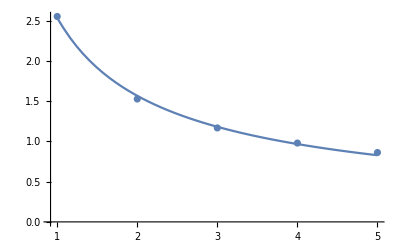

```mathematica
Show[ListPlot[{{1,f1[[1,2]]},{2,f2[[1,2]]},{3,f3[[1,2]]},{4,f4[[1,2]]},{5,f5[[1,2]]}}],Plot[fitU[x],{x,1,5}]]
```

```mathematica
Abs[fit2U[5,datatot5[nn+1][[p1,1]]]/datatot5[nn+1][[p1,4]]-1]100//Max
Abs[fit2U[4,datatot4[nn+1][[p2,1]]]/datatot4[nn+1][[p2,4]]-1]100//Max
Abs[fit2U[3,datatot3[nn+1][[p3,1]]]/datatot3[nn+1][[p3,4]]-1]100//Max
Abs[fit2U[2,datatot2[nn+1][[p4,1]]]/datatot2[nn+1][[p4,4]]-1]100//Max
Abs[fit2U[1,datatot[nn+1][[p5,1]]]/datatot[nn+1][[p5,4]]-1]100//Max
```

0.0353456

0.0178169

0.0460172

0.0837444

0.0947851

## Fluxes

#### Change of variables [not needed anymore]

```mathematica
ruleslog={ψ''[r]->D[ψ[Log[r]],{r,2}],ψ'[r]->D[ψ[Log[r]],r],m'[r]->D[m[Log[r]],r],F'[r]->D[F[Log[r]],r]};
```

```mathematica
Import["./src/master_axial.m"][[1]]//.ruleslog//.{Log[r]->xx,ψ[r]->ψ[xx],F[r]->F[xx],m[r]->F[xx],r->ss};
%//.ss->Exp[r];
newmaster=Collect[%//.{xx->r},{ψ''[r],ψ'[r],ψ[r]},FullSimplify]
```

ψ[r] (ω^2-ⅇ^(-3 r) F[r] (ⅇ^r ℓ (1+ℓ)-6 F[r]+m'[r]))-ⅇ^(-3 r) F[r] (ⅇ^r-4 F[r]+m'[r]) ψ'[r]+ⅇ^(-3 r) (ⅇ^r-2 F[r]) F[r] ψ''[r]

```mathematica
Import["./src/master_axial.m"][[2]]//.ruleslog//.{Log[r]->xx,ψ[r]->ψ[xx],F[r]->F[xx],m[r]->F[xx],r->ss};
%//.ss->Exp[r];
newsource=Collect[%//.{xx->r},{ψ''[r],ψ'[r],ψ[r]},Simplify];
```

```mathematica
Import["./src/master_axial.m"][[1]]//.{ψ[r]->Exp[I ω rt[r]]ψb[r],D[ψ[r]->Exp[I ω rt[r]]ψb[r],r],D[ψ[r]->Exp[I ω rt[r]]ψb[r],{r,2}],rt'[r]->1/Sqrt[F[r](1-2m[r]/r)],D[rt'[r]->1/Sqrt[F[r](1-2m[r]/r)],r],F'[r]->Import["./src/rulesmetric.m"][[2]]};
newmasterH=Collect[%ⅇ^(-ⅈ rt[r] ω)//.{ψb[r]->ψ[r],D[ψb[r]->ψ[r],r],D[ψb[r]->ψ[r],{r,2}]},{ψ''[r],ψ'[r],ψ[r],ω},FullSimplify]
newmasterH//.ruleslog//.{Log[r]->xx,ψ[r]->ψ[xx],F[r]->F[xx],m[r]->F[xx],r->ss};
%//.ss->Exp[r];
newmasterHLog=Collect[%//.{xx->r},{ψ''[r],ψ'[r],ψ[r]},FullSimplify]
```

-(F[r] ψ[r] (-6 m[r]+r (ℓ+ℓ^2+m'[r])))/r^3+(2 ⅈ ω √((F[r] (r-2 m[r]))/r)+(F[r] (2 m[r]-r m'[r]))/r^2) ψ'[r]+(F[r] (r-2 m[r]) ψ''[r])/r

-ⅇ^(-3 r) F[r] ψ[r] (ⅇ^r ℓ (1+ℓ)-6 F[r]+m'[r])+ⅇ^(-3 r) (4 F[r]^2+2 ⅈ ⅇ^(2 r) ω √(F[r]-2 ⅇ^-r F[r]^2)-F[r] (ⅇ^r+m'[r])) ψ'[r]+ⅇ^(-3 r) (ⅇ^r-2 F[r]) F[r] ψ''[r]

```mathematica
Export["./src/master_axial.m",{Import["./src/master_axial.m"][[1]],Import["./src/master_axial.m"][[2]],newmaster,newsource,newmasterH,newmasterHLog}]
```

./src/master_axial.m

#### Tables

```mathematica
{FluxGen[2,1,8,10^3,"HQ",100,10^5],FluxGen[2,1,8,10^3,"NFW",100,{10^5,10^5}],FluxGen[2,1,8,10^3,"NFW",100,{10^5,5 10^5}],FluxGen[2,1,8,10^3,"Ein",100,{10^5,10^13}]}
```

{7.801896207814368173172531×10^-7,7.777104885688631832695695×10^-7,7.803934036814736206904391×10^-7,7.764208863798954008372736×10^-7}

```mathematica
{FluxGen[3,2,8,10^3,"HQ",100,10^5],FluxGen[3,2,8,10^3,"NFW",100,{10^5,10^5}],FluxGen[3,2,8,10^3,"NFW",100,{10^5,5 10^5}],FluxGen[3,2,8,10^3,"Ein",100,{10^5,10^13}]}
```

```mathematica
{FluxGen[4,1,8,10^3,"HQ",100,10^5],FluxGen[4,1,8,10^3,"NFW",100,{10^5,10^5}],FluxGen[4,1,8,10^3,"NFW",100,{10^5,5 10^5}],FluxGen[4,1,8,10^3,"Ein",100,{10^5,10^13}]}
```

```mathematica
{FluxGen[4,3,8,10^3,"HQ",100,10^5],FluxGen[4,3,8,10^3,"NFW",100,{10^5,10^5}],FluxGen[4,3,8,10^3,"NFW",100,{10^5,5 10^5}],FluxGen[4,3,8,10^3,"Ein",100,{10^5,10^13}]}
```

```mathematica
(* --- *)
```

```mathematica
{FluxGen[2,1,8,10^3,"HQ",100,10^3],FluxGen[2,1,8,10^3,"NFW",100,{10^3,10^3}],FluxGen[2,1,8,10^3,"NFW",100,{10^3,5 10^3}],FluxGen[2,1,8,10^3,"Ein",100,{10^3,10^13}]}
```

{6.3598145146950669405582185×10^-7,4.3470344679386095094310751×10^-7,6.5338364293484134774387789×10^-7,4.1167561010100520305555289×10^-7}

```mathematica
{FluxGen[3,2,8,10^3,"HQ",100,10^3],FluxGen[3,2,8,10^3,"NFW",100,{10^3,10^3}],FluxGen[3,2,8,10^3,"NFW",100,{10^3,5 10^3}],FluxGen[3,2,8,10^3,"Ein",100,{10^3,10^13}]}
```

{1.9544825203839004091106168×10^-7,1.3408428343171115316452346×10^-7,2.0060023468329066565294742×10^-7,1.3084863710022994268833905×10^-7}

```mathematica
{FluxGen[4,1,8,10^3,"HQ",100,10^3],FluxGen[4,1,8,10^3,"NFW",100,{10^3,10^3}],FluxGen[4,1,8,10^3,"NFW",100,{10^3,5 10^3}],FluxGen[4,1,8,10^3,"Ein",100,{10^3,10^13}]}
```

{6.0233807308325177323791562×10^-13,3.6127612448688395902136521×10^-13,6.4032973204223940623858194×10^-13,1.6413154318928833197901742×10^-13}

```mathematica
{FluxGen[4,3,8,10^3,"HQ",100,10^3],FluxGen[4,3,8,10^3,"NFW",100,{10^3,10^3}],FluxGen[4,3,8,10^3,"NFW",100,{10^3,5 10^3}],FluxGen[4,3,8,10^3,"Ein",100,{10^3,10^13}]}
```

{4.4570039822368457625486329×10^-8,3.0668322728091271103308997×10^-8,4.5705920828671121357430749×10^-8,3.0968375426650352209926045×10^-8}

### redshift dependence

```mathematica
<<Teukolsky`
<<KerrGeodesics`
```

```mathematica
omega[rp_,solg_]:=Sqrt[(F[rp] m[rp])/(rp^2-2 rp m[rp])] 1/Sqrt[rp]//.{F->solg[[1,2]],m->solg[[3,2]]}
```

```mathematica
finrp[val_?NumberQ,solg_]:=FindRoot[omega[rp,solg]==val,{rp,7},WorkingPrecision->50][[1,2]]
Off[InterpolatingFunction::dmval]
```

```mathematica
bHQ0=background["HQ",10^2,10^3,10^13][[1]];
bNFW0=background["NFW",10^2,{10^3,5 10^3},10^13][[1]];
bEin0=background["Ein",10^2,{10^3,10^13},10^13][[1]];
```

```mathematica
bHQ1=background["HQ",10^2,10^4,10^13][[1]];
bNFW1=background["NFW",10^2,{10^4,5 10^4},10^13][[1]];
bEin1=background["Ein",10^2,{10^4,10^13},10^13][[1]];
```

```mathematica
bHQ1v2=background["HQ",10^2,10^5,10^13][[1]];
bNFW1v2=background["NFW",10^2,{10^5,5 10^5},10^13][[1]];
bEin1v2=background["Ein",10^2,{10^5,10^13},10^13][[1]];
```

```mathematica
bHQ1v3=background["HQ",10^2,10^6,10^13][[1]];
bNFW1v3=background["NFW",10^2,{10^6,5 10^6},10^13][[1]];
bEin1v3=background["Ein",10^2,{10^6,10^13},10^13][[1]];
```

```mathematica
rangefreq=N[Range[Log10[5/1000],Log10[55/1000],(Log10[55/1000]-Log10[5/1000])/10],70];
```

```mathematica
rpvac=Table[FindRoot[rp^(-3/2)==10^rangefreq[[i]],{rp,7},WorkingPrecision->50][[1,2]],{i,1,Length[rangefreq]}];

rpHQ0=Table[finrp[10^rangefreq[[i]],bHQ0],{i,1,Length[rangefreq]}];
rpNFW0=Table[finrp[10^rangefreq[[i]],bNFW0],{i,1,Length[rangefreq]}];
rpEin0=Table[finrp[10^rangefreq[[i]],bEin0],{i,1,Length[rangefreq]}];

rpHQ1=Table[finrp[10^rangefreq[[i]],bHQ1],{i,1,Length[rangefreq]}];
rpNFW1=Table[finrp[10^rangefreq[[i]],bNFW1],{i,1,Length[rangefreq]}];
rpEin1=Table[finrp[10^rangefreq[[i]],bEin1],{i,1,Length[rangefreq]}];

rpHQ1v2=Table[finrp[10^rangefreq[[i]],bHQ1v2],{i,1,Length[rangefreq]}];
rpNFW1v2=Table[finrp[10^rangefreq[[i]],bNFW1v2],{i,1,Length[rangefreq]}];
rpEin1v2=Table[finrp[10^rangefreq[[i]],bEin1v2],{i,1,Length[rangefreq]}];

rpHQ1v3=Table[finrp[10^rangefreq[[i]],bHQ1v3],{i,1,Length[rangefreq]}];
rpNFW1v3=Table[finrp[10^rangefreq[[i]],bNFW1v3],{i,1,Length[rangefreq]}];
rpEin1v3=Table[finrp[10^rangefreq[[i]],bEin1v3],{i,1,Length[rangefreq]}];
```

```mathematica
ParallelNeeds["HaloFlux`"]
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
dataHQ0=ParallelTable[{rpHQ0[[i]],FluxGen[2,1,rpHQ0[[i]],10^3,"HQ",10^2,10^3]},{i,1,Length[rpHQ0]}];
```

```mathematica
dataNFW0=ParallelTable[{rpNFW0[[i]],FluxGen[2,1,rpNFW0[[i]],10^3,"NFW",10^2,{10^3,5 10^3}]},{i,1,Length[rpNFW0]}];
```

```mathematica
dataEin0=ParallelTable[{rpEin0[[i]],FluxGen[2,1,rpEin0[[i]],10^3,"Ein",10^2,{10^3,10^13}]},{i,1,Length[rpEin0]}];
```

```mathematica
Export["./data/fluxesvsomega_M1d2a01d3.m",{dataHQ0,dataNFW0,dataEin0}]
```

./data/fluxesvsomega_M1d2a01d3.m

```mathematica
dataHQ1=ParallelTable[{rpHQ1[[i]],FluxGen[2,1,rpHQ1[[i]],10^3,"HQ",10^2,10^4]},{i,1,Length[rpHQ1]}];
```

```mathematica
dataNFW1=ParallelTable[{rpNFW1[[i]],FluxGen[2,1,rpNFW1[[i]],10^3,"NFW",10^2,{10^4,5 10^4}]},{i,1,Length[rpNFW1]}];
```

```mathematica
dataEin1=ParallelTable[{rpEin1[[i]],FluxGen[2,1,rpEin1[[i]],10^3,"Ein",10^2,{10^4,10^13}]},{i,1,Length[rpEin1]}];
```

```mathematica
Export["./data/fluxesvsomega_M1d2a01d4.m",{dataHQ1,dataNFW1,dataEin1}]
```

./data/fluxesvsomega_M1d2a01d4.m

```mathematica
dataHQ1v2=ParallelTable[{rpHQ1v2[[i]],FluxGen[2,1,rpHQ1v2[[i]],10^3,"HQ",10^2,10^5]},{i,1,Length[rpHQ1v2]}];
```

```mathematica
dataNFW1v2=ParallelTable[{rpNFW1v2[[i]],FluxGen[2,1,rpNFW1v2[[i]],10^3,"NFW",10^2,{10^5,5 10^5}]},{i,1,Length[rpNFW1v2]}];
```

```mathematica
dataEin1v2=ParallelTable[{rpEin1v2[[i]],FluxGen[2,1,rpEin1v2[[i]],10^3,"Ein",10^2,{10^5,10^13}]},{i,1,Length[rpEin1v2]}];
```

```mathematica
Export["./data/fluxesvsomega_M1d2a01d5.m",{dataHQ1v2,dataNFW1v2,dataEin1v2}]
```

./data/fluxesvsomega_M1d2a01d5.m

```mathematica
dataHQ1v3=ParallelTable[{rpHQ1v3[[i]],FluxGen[prec->20,2,1,rpHQ1v3[[i]],10^3,"HQ",10^2,10^6]},{i,1,Length[rpHQ1v3]}];
```

```mathematica
dataNFW1v3=ParallelTable[{rpNFW1v3[[i]],FluxGen[prec->20,2,1,rpNFW1v3[[i]],10^3,"NFW",10^2,{10^6,5 10^6}]},{i,1,Length[rpNFW1v3]}];
```

```mathematica
dataEin1v3=ParallelTable[{rpEin1v3[[i]],FluxGen[prec->20,2,1,rpEin1v3[[i]],10^3,"Ein",10^2,{10^6,10^13}]},{i,1,Length[rpEin1v3]}];
```

```mathematica
Export["./data/fluxesvsomega_M1d2a01d6.m",{dataHQ1v3,dataNFW1v3,dataEin1v3}]
```

./data/fluxesvsomega_M1d2a01d6.m

```mathematica
{dataHQ0,dataNFW0,dataEin0}=Import["./data/fluxesvsomega_M1d2a01d3.m"];
{dataHQ1,dataNFW1,dataEin1}=Import["./data/fluxesvsomega_M1d2a01d4.m"];
{dataHQ1v2,dataNFW1v2,dataEin1v2}=Import["./data/fluxesvsomega_M1d2a01d5.m"];
{dataHQ1v3,dataNFW1v3,dataEin1v3}=Import["./data/fluxesvsomega_M1d2a01d6.m"];
```

```mathematica
orbitvac=KerrGeoOrbit[0,#,0,1]&/@rpvac;
modevac=Monitor[Table[TeukolskyPointParticleMode[-2,2,1,0,0,orbitvac[[i]]],{i,1,Length[orbitvac]}],i];
```

```mathematica
diffred[x_,data1_,data2_,fact_,z_]:=Abs[Interpolation[Thread[{10^rangefreq,data1[[All,2]]}]][x]/((1-fact z)^2 Interpolation[Table[{10^rangefreq[[i]],2data2[[i]]["Fluxes"][[1,1]]},{i,1,Length[orbitvac]}]][x(1+fact z)])-1]100;
```

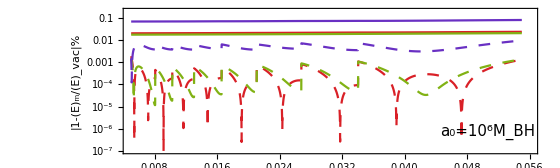

```mathematica
xl=Join[Table[{0.0000001i,,{0.012,0}},{i,0,9}],Table[{0.000001i,,{0.012,0}},{i,0,9}],Table[{0.00001i,,{0.012,0}},{i,0,9}],Table[{0.0001i,,{0.012,0}},{i,0,9}],Table[{0.001i,,{0.012,0}},{i,0,9}],Table[{0.01i,,{0.012,0}},{i,0,9}],Table[{0.1i,,{0.012,0}},{i,0,9}],Table[{1i,,{0.012,0}},{i,0,9}],Table[{10i,,{0.012,0}},{i,0,9}],Table[{100i,,{0.012,0}},{i,0,9}],{{100,"100",{0.02,0}},{10,,{0.02,0}},{1,"1",{0.02,0}},{0.1,,{0.02,0}},{0.01,"10^-2",{0.02,0}},{0.001,,{0.02,0}},{0.0001,"10^-4",{0.02,0}},{0.00001,,{0.02,0}},{0.000001,"10^-6",{0.02,0}}}];

xr=Join[Table[{0.0000001i,,{0.012,0}},{i,0,9}],Table[{0.000001i,,{0.012,0}},{i,0,9}],Table[{0.00001i,,{0.012,0}},{i,0,9}],Table[{0.0001i,,{0.012,0}},{i,0,9}],Table[{0.001i,,{0.012,0}},{i,0,9}],Table[{0.01i,,{0.012,0}},{i,0,9}],Table[{0.1i,,{0.012,0}},{i,0,9}],Table[{1i,,{0.012,0}},{i,0,9}],Table[{10i,,{0.012,0}},{i,0,9}],Table[{100i,,{0.012,0}},{i,0,9}],{{100,,{0.02,0}},{10,,{0.02,0}},{1,,{0.02,0}},{0.1,,{0.02,0}},{0.01,,{0.02,0}},{0.001,,{0.02,0}},{0.0001,,{0.02,0}},{0.00001,,{0.02,0}},{0.000001,,{0.02,0}}}];

xb=Join[Table[{0.01i/5,,{0.012,0}},{i,0,100}],Table[{0.01i,Integerise[0.01i],{0.02,0}},{i,0,100}]];
xu=Join[Table[{0.01i/5,,{0.012,0}},{i,0,100}],Table[{0.01i,,{0.02,0}},{i,0,100}]];

Δ={diffred[x,dataHQ1v3,modevac,1,10^-4],diffred[x,dataNFW1v3,modevac,1,10^-4],diffred[x,dataEin1v3,modevac,1,10^-4]};
Δ0={diffred[x,dataHQ1v3,modevac,0,10^-4],diffred[x,dataNFW1v3,modevac,0,10^-4],diffred[x,dataEin1v3,modevac,0,10^-4]};
Δ1={diffred[x,dataHQ1v3,modevac,1,10^-4],diffred[x,dataNFW1v3,modevac,0.8613376299645527,10^-4],diffred[x,dataEin1v3,modevac,3.18073695890666237635907174001787807218`24.355184680670167,10^-4]};

p1=LogPlot[{Δ1[[1]],Δ1[[2]],Δ1[[3]],Δ0[[1]],Δ0[[2]],Δ0[[3]]},{x,0.005,0.055},Frame->True,FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],ImageSize->560,PlotRange->{{0.005,0.056},{10^-7,0.2}},PlotStyle->{Directive[Comb2[[1]],Dashing[{0.015,0.015}]],Directive[Comb1[[2]],Dashing[{0.015,0.015}]],Directive[Comb3[[2]],Dashing[{0.015,0.015}]],Comb2[[1]],Comb1[[2]],Comb3[[2]]},FrameLabel->{{Style["|1-(Ė)_m/(Ė)_vac|%",20],None},{None,None}},Epilog->leg["a_0=10^6M_BH",15,0,0.88,0.15,Black],ImagePadding->{{85, 40}, {55, 1}},AspectRatio->0.3,FrameTicks->{{xl,xr},{xu,xu}}]
```

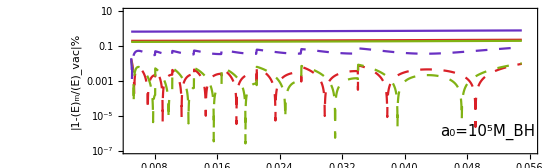

```mathematica
Δ={diffred[x,dataHQ1v2,modevac,1,10^-3],diffred[x,dataNFW1v2,modevac,1,10^-3],diffred[x,dataEin1v2,modevac,1,10^-3]};
Δ0={diffred[x,dataHQ1v2,modevac,0,10^-3],diffred[x,dataNFW1v2,modevac,0,10^-3],diffred[x,dataEin1v2,modevac,0,10^-3]};
Δ1={diffred[x,dataHQ1v2,modevac,1,10^-3],diffred[x,dataNFW1v2,modevac,0.8613376299645527,10^-3],diffred[x,dataEin1v2,modevac,3.18073695890666237635907174001787807218`24.355184680670167,10^-3]};

p2=LogPlot[{Δ1[[1]],Δ1[[2]],Δ1[[3]],Δ0[[1]],Δ0[[2]],Δ0[[3]]},{x,0.005,0.055},Frame->True,FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],ImageSize->560,PlotRange->{{0.005,0.056},{10^-7,10}},PlotStyle->{Directive[Comb2[[1]],Dashing[{0.015,0.015}]],Directive[Comb1[[2]],Dashing[{0.015,0.015}]],Directive[Comb3[[2]],Dashing[{0.015,0.015}]],Comb2[[1]],Comb1[[2]],Comb3[[2]]},FrameLabel->{{Style["|1-(Ė)_m/(Ė)_vac|%",20],None},{None,None}},Epilog->leg["a_0=10^5M_BH",15,0,0.88,0.15,Black],ImagePadding->{{85, 40}, {55, 1}},AspectRatio->0.3,FrameTicks->{{xl,xr},{xu,xu}}]
```

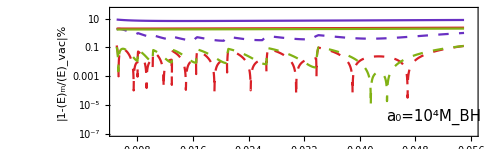

```mathematica
xl=Join[Table[{0.0000001i,,{0.012,0}},{i,0,9}],Table[{0.000001i,,{0.012,0}},{i,0,9}],Table[{0.00001i,,{0.012,0}},{i,0,9}],Table[{0.0001i,,{0.012,0}},{i,0,9}],Table[{0.001i,,{0.012,0}},{i,0,9}],Table[{0.01i,,{0.012,0}},{i,0,9}],Table[{0.1i,,{0.012,0}},{i,0,9}],Table[{1i,,{0.012,0}},{i,0,9}],Table[{10i,,{0.012,0}},{i,0,9}],Table[{100i,,{0.012,0}},{i,0,9}],{{100,"100",{0.02,0}},{10,,{0.02,0}},{1,"1",{0.02,0}},{0.1,,{0.02,0}},{0.01,"10^-2",{0.02,0}},{0.001,,{0.02,0}},{0.0001,"10^-4",{0.02,0}},{0.00001,,{0.02,0}},{0.000001,"10^-6",{0.02,0}}}];

xr=Join[Table[{0.0000001i,,{0.012,0}},{i,0,9}],Table[{0.000001i,,{0.012,0}},{i,0,9}],Table[{0.00001i,,{0.012,0}},{i,0,9}],Table[{0.0001i,,{0.012,0}},{i,0,9}],Table[{0.001i,,{0.012,0}},{i,0,9}],Table[{0.01i,,{0.012,0}},{i,0,9}],Table[{0.1i,,{0.012,0}},{i,0,9}],Table[{1i,,{0.012,0}},{i,0,9}],Table[{10i,,{0.012,0}},{i,0,9}],Table[{100i,,{0.012,0}},{i,0,9}],{{100,,{0.02,0}},{10,,{0.02,0}},{1,,{0.02,0}},{0.1,,{0.02,0}},{0.01,,{0.02,0}},{0.001,,{0.02,0}},{0.0001,,{0.02,0}},{0.00001,,{0.02,0}},{0.000001,,{0.02,0}}}];

Δ={diffred[x,dataHQ1,modevac,1,10^-2],diffred[x,dataNFW1,modevac,1,10^-2],diffred[x,dataEin1,modevac,1,10^-2]};
Δ0={diffred[x,dataHQ1,modevac,0,10^-2],diffred[x,dataNFW1,modevac,0,10^-2],diffred[x,dataEin1,modevac,0,10^-2]};
Δ1={diffred[x,dataHQ1,modevac,1,10^-2],diffred[x,dataNFW1,modevac,0.8613376299645527,10^-2],diffred[x,dataEin1,modevac,3.18073695890666237635907174001787807218`24.355184680670167,10^-2]};

p3=LogPlot[{Δ1[[1]],Δ1[[2]],Δ1[[3]],Δ0[[1]],Δ0[[2]],Δ0[[3]]},{x,0.005,0.055},Frame->True,FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],ImageSize->498,PlotRange->{{0.005,0.056},{10^-7,40}},PlotStyle->{Directive[Comb2[[1]],Dashing[{0.015,0.015}]],Directive[Comb1[[2]],Dashing[{0.015,0.015}]],Directive[Comb3[[2]],Dashing[{0.015,0.015}]],Comb2[[1]],Comb1[[2]],Comb3[[2]]},FrameLabel->{{Style["|1-(Ė)_m/(Ė)_vac|%",20],None},{None,None}},Epilog->leg["a_0=10^4M_BH",15,0,0.88,0.15,Black],ImagePadding->{{85, 40}, {55, 1}},AspectRatio->0.3,FrameTicks->{{xl,xr},{xu,xu}},PlotLegends->Placed[LineLegend[{Style["Hernquist",13],Style["NFW",13],Style["Einasto",13]},LegendLayout->(Grid[{Flatten@Riffle[#,Spacer[3]]}]&)],Scaled[{0.38,0.16}]]]
```

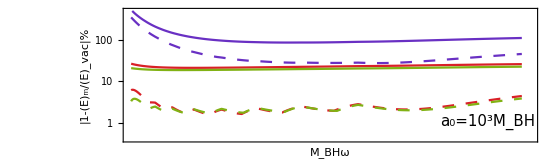

```mathematica
xl=Join[Table[{0.0000001i,,{0.012,0}},{i,0,9}],Table[{0.000001i,,{0.012,0}},{i,0,9}],Table[{0.00001i,,{0.012,0}},{i,0,9}],Table[{0.0001i,,{0.012,0}},{i,0,9}],Table[{0.001i,,{0.012,0}},{i,0,9}],Table[{0.01i,,{0.012,0}},{i,0,9}],Table[{0.1i,,{0.012,0}},{i,0,9}],Table[{1i,,{0.012,0}},{i,0,9}],Table[{10i,,{0.012,0}},{i,0,9}],Table[{100i,,{0.012,0}},{i,0,9}],{{100,"100",{0.02,0}},{10,"10",{0.02,0}},{1,"1",{0.02,0}},{0.1,,{0.02,0}},{0.01,"10^-2",{0.02,0}},{0.001,,{0.02,0}},{0.0001,"10^-4",{0.02,0}},{0.00001,,{0.02,0}},{0.000001,"10^-6",{0.02,0}}}];

xr=Join[Table[{0.0000001i,,{0.012,0}},{i,0,9}],Table[{0.000001i,,{0.012,0}},{i,0,9}],Table[{0.00001i,,{0.012,0}},{i,0,9}],Table[{0.0001i,,{0.012,0}},{i,0,9}],Table[{0.001i,,{0.012,0}},{i,0,9}],Table[{0.01i,,{0.012,0}},{i,0,9}],Table[{0.1i,,{0.012,0}},{i,0,9}],Table[{1i,,{0.012,0}},{i,0,9}],Table[{10i,,{0.012,0}},{i,0,9}],Table[{100i,,{0.012,0}},{i,0,9}],{{100,,{0.02,0}},{10,,{0.02,0}},{1,,{0.02,0}},{0.1,,{0.02,0}},{0.01,,{0.02,0}},{0.001,,{0.02,0}},{0.0001,,{0.02,0}},{0.00001,,{0.02,0}},{0.000001,,{0.02,0}}}];

Δ={diffred[x,dataHQ0,modevac,1,10^-1],diffred[x,dataNFW0,modevac,1,10^-1],diffred[x,dataEin0,modevac,1,10^-1]};
Δ0={diffred[x,dataHQ0,modevac,0,10^-1],diffred[x,dataNFW0,modevac,0,10^-1],diffred[x,dataEin0,modevac,0,10^-1]};
Δ1={diffred[x,dataHQ0,modevac,1,10^-1],diffred[x,dataNFW0,modevac,0.8613376299645527,10^-1],diffred[x,dataEin0,modevac,3.18073695890666237635907174001787807218`24.355184680670167,10^-1]};

p4=LogPlot[{Δ1[[1]],Δ1[[2]],Δ1[[3]],Δ0[[1]],Δ0[[2]],Δ0[[3]]},{x,0.005,0.055},Frame->True,FrameStyle->Directive[16,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],ImageSize->560,PlotRange->{{0.005,0.056},{0.4,500}},PlotStyle->{Directive[Comb2[[1]],Dashing[{0.015,0.015}]],Directive[Comb1[[2]],Dashing[{0.015,0.015}]],Directive[Comb3[[2]],Dashing[{0.015,0.015}]],Comb2[[1]],Comb1[[2]],Comb3[[2]]},FrameLabel->{{Style["|1-(Ė)_m/(Ė)_vac|%",20],None},{Style["M_BHω",22],None}},Epilog->leg["a_0=10^3M_BH",15,0,0.88,0.15,Black],ImagePadding->{{85, 40}, {55, 1}},AspectRatio->0.3,FrameTicks->{{xl,xr},{xb,xu}}]
```

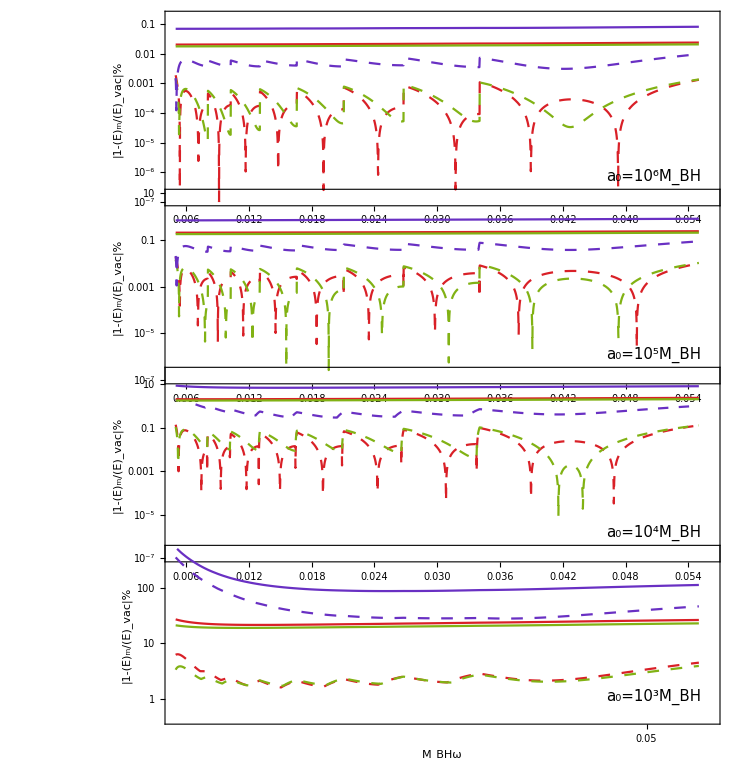

./plot/Fig5.pdf

```mathematica
GraphicsColumn[{p1,p2,p3,p4},Spacings->-35,ImageSize->750,ImagePadding->{{0, 0}, {55, 20}}]
Export["./plot/Fig5.pdf",%]
```

### Convergence tests

```mathematica
omega[rp_,solg_]:=Sqrt[(F[rp] m[rp])/(rp^2-2 rp m[rp])] 1/Sqrt[rp]//.{F->solg[[1,2]],m->solg[[3,2]]}
```

```mathematica
finrp[val_?NumberQ,solg_]:=FindRoot[omega[rp,solg]==val,{rp,7},WorkingPrecision->50][[1,2]]
Off[InterpolatingFunction::dmval]
```

```mathematica
bHQ0=background["HQ",10^2,10^3,10^13][[1]];
bNFW0=background["NFW",10^2,{10^3,5 10^3},10^13][[1]];
bEin0=background["Ein",10^2,{10^3,10^13},10^13][[1]];
```

```mathematica
bHQ1=background["HQ",10^2,10^4,10^13][[1]];
bNFW1=background["NFW",10^2,{10^4,5 10^4},10^13][[1]];
bEin1=background["Ein",10^2,{10^4,10^13},10^13][[1]];
```

```mathematica
bHQ1v2=background["HQ",10^2,10^5,10^13][[1]];
bNFW1v2=background["NFW",10^2,{10^5,5 10^5},10^13][[1]];
bEin1v2=background["Ein",10^2,{10^5,10^13},10^13][[1]];
```

```mathematica
bHQ1v3=background["HQ",10^2,10^6,10^13][[1]];
bNFW1v3=background["NFW",10^2,{10^6,5 10^6},10^13][[1]];
bEin1v3=background["Ein",10^2,{10^6,10^13},10^13][[1]];
```

```mathematica
rangefreq=N[Range[Log10[5/1000],Log10[55/1000],(Log10[55/1000]-Log10[5/1000])/10],70];
```

```mathematica
rpvac=Table[FindRoot[rp^(-3/2)==10^rangefreq[[i]],{rp,7},WorkingPrecision->50][[1,2]],{i,1,Length[rangefreq]}];

rpHQ0=Table[finrp[10^rangefreq[[i]],bHQ0],{i,1,Length[rangefreq]}];
rpNFW0=Table[finrp[10^rangefreq[[i]],bNFW0],{i,1,Length[rangefreq]}];
rpEin0=Table[finrp[10^rangefreq[[i]],bEin0],{i,1,Length[rangefreq]}];

rpHQ1=Table[finrp[10^rangefreq[[i]],bHQ1],{i,1,Length[rangefreq]}];
rpNFW1=Table[finrp[10^rangefreq[[i]],bNFW1],{i,1,Length[rangefreq]}];
rpEin1=Table[finrp[10^rangefreq[[i]],bEin1],{i,1,Length[rangefreq]}];

rpHQ1v2=Table[finrp[10^rangefreq[[i]],bHQ1v2],{i,1,Length[rangefreq]}];
rpNFW1v2=Table[finrp[10^rangefreq[[i]],bNFW1v2],{i,1,Length[rangefreq]}];
rpEin1v2=Table[finrp[10^rangefreq[[i]],bEin1v2],{i,1,Length[rangefreq]}];

rpHQ1v3=Table[finrp[10^rangefreq[[i]],bHQ1v3],{i,1,Length[rangefreq]}];
rpNFW1v3=Table[finrp[10^rangefreq[[i]],bNFW1v3],{i,1,Length[rangefreq]}];
rpEin1v3=Table[finrp[10^rangefreq[[i]],bEin1v3],{i,1,Length[rangefreq]}];
```

```mathematica
test1=FluxGen[2,1,rpHQ0[[1]],10^4,"HQ",10^2,10^3]
test2=FluxGen[2,1,rpHQ0[[-1]],10^4,"HQ",10^2,10^3]
```

1.402157115569129954322834×10^-10

2.50627028198343176368913×10^-6

```mathematica
Import["./data/fluxesvsomega_M1d2a01d3.m"][[1,1,2]]/test1-1
Import["./data/fluxesvsomega_M1d2a01d3.m"][[1,-1,2]]/test2-1
```

3.15231152026165834×10^-6

4.392243613606562936×10^-6

```mathematica
test3=FluxGen[2,1,rpHQ1[[1]],10^4,"HQ",10^2,10^4]
test4=FluxGen[2,1,rpHQ1[[-1]],10^4,"HQ",10^2,10^4]
```

1.128528948288478531512619×10^-10

2.034021040761872008889982×10^-6

```mathematica
Import["./data/fluxesvsomega_M1d2a01d4.m"][[1,1,2]]/test3-1
Import["./data/fluxesvsomega_M1d2a01d4.m"][[1,-1,2]]/test4-1
```

2.77675518124951701×10^-6

1.965736176290930726×10^-6

```mathematica
(* ----- *)
```

```mathematica
test1=FluxGen[2,1,rpNFW0[[1]],10^4,"NFW",10^2,{10^3,5 10^3}]
test2=FluxGen[2,1,rpNFW0[[-1]],10^4,"NFW",10^2,{10^3,5 10^3}]
```

2.0000000000000000000003470577863010637537380866901×10^6

1.337446089718866586812396×10^-10

1.8181818181818181818183958609057466337759201412330×10^5

2.438106981925786431796175×10^-6

```mathematica
Import["./data/fluxesvsomega_M1d2a01d3.m"][[2,1,2]]/test1-1
Import["./data/fluxesvsomega_M1d2a01d3.m"][[2,-1,2]]/test2-1
```

2.9560462401685862159×10^-6

5.65875025492525388×10^-6

```mathematica
test3=FluxGen[2,1,rpNFW1[[1]],10^4,"NFW",10^2,{10^4,5 10^4}]
test4=FluxGen[2,1,rpNFW1[[-1]],10^4,"NFW",10^2,{10^4,5 10^4}]
```

1.9999999999999999999997557248290991236237535031464×10^6

1.125556772199165730419828×10^-10

1.8181818181818181818178183222104869626457558433012×10^5

2.027958291544236975015438×10^-6

```mathematica
Import["./data/fluxesvsomega_M1d2a01d4.m"][[2,1,2]]/test3
Import["./data/fluxesvsomega_M1d2a01d4.m"][[2,-1,2]]/test4
```

1.000002710295557349805649

1.000002256581685799102576

```mathematica
(* ----- *)
```

```mathematica
test1=FluxGen[2,1,rpEin0[[1]],10^4,"Ein",10^2,{10^3,10^13}]
test2=FluxGen[2,1,rpEin0[[-1]],10^4,"Ein",10^2,{10^3,10^13}]
```

1.9999999999999999999973023129101023481462814337075×10^6

6.998762795143843978356825×10^-10

1.8181818181818181818135845171634082242631864693750×10^5

4.203591108010041076591462×10^-6

```mathematica
Import["./data/fluxesvsomega_M1d2a01d3.m"][[3,1,2]]/test1-1
Import["./data/fluxesvsomega_M1d2a01d3.m"][[3,-1,2]]/test2-1
```

2.740178793567587773×10^-6

5.568280571680564386×10^-6

```mathematica
test3=FluxGen[2,1,rpEin1[[1]],10^4,"Ein",10^2,{10^4,10^13}]
test4=FluxGen[2,1,rpEin1[[-1]],10^4,"Ein",10^2,{10^4,10^13}]
```

1.9999999999999999999999081705387103286173670021796×10^6

1.2011543704019602173868354×10^-10

1.8181818181818181818179711557301861174252547119220×10^5

2.14709897377090750628537×10^-6

```mathematica
Import["./data/fluxesvsomega_M1d2a01d4.m"][[3,1,2]]/test3-1
Import["./data/fluxesvsomega_M1d2a01d4.m"][[3,-1,2]]/test4-1
```

2.910322694569795209×10^-6

2.253853431108887209×10^-6